# STIRAP

P. Huft

## functions

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"\\images\\"}]];
```

```mathematica
BuildSchroedingerSystem[H_,psi0_,t0_:0]:=Module[
{hamiltonian=H,ψ0=psi0,ψ,statelength,eqs,ics,sys,P,i},
statelength = Length[ψ0];
ψ = Array[Subscript[P, #][t]&,statelength];
eqs = {};(*system to solve*)
ics = {};(*initial conditions*)
For[i=1,i<statelength+1,i++,
AppendTo[eqs,D[ψ[[i]],t]==-ⅈ (hamiltonian.ψ)[[i]]];
AppendTo[ics,(ψ[[i]]/.t->t0)==ψ0[[i]]];
];
sys = Flatten@Join[eqs,ics];
{ψ,sys}
];

(*R is the angular momentum bector which experiences the torque vector γ*)
TorqueVectorSphere[Rx_,Ry_,Rz_,γx_,γy_,γz_]:=Graphics3D[{{Specularity[Pink,5],Opacity[0.1],Sphere[]},{Red,Thick,Arrow[{{0,0,0},{Rx,Ry,Rz}}]},{Blue,Thick,Dashed,Line[{{0,0,0},{Rx,Ry,0}}]},
{Blue,Thick,Dashed,Line[{{Rx,Ry,0},{Rx,Ry,Rz}}]},{Green,Thick,Dashed,Line[{{0,0,0},{0,0,Rz}}]},
{Green,Thick,Dashed,Line[{{0,0,Rz},{Rx,Ry,Rz}}]},
{Purple,Thick,Arrow[{{0,0,0},{γx,γy,γz}}]},
Text[Style["3",20],{0,0,1.3}],Text[Style["1",20],{1.3,0,0}],Text[Style["2",20],{0,1.3,0}]},Boxed->False,Axes->True,AxesOrigin->{0,0,0},ImageSize->Medium];
```

## classic 3-level Λ scheme

STIRAP

```mathematica
w=1.5;
μ=2.5;
Ω0=6π;
Ω1[t_]:=Ω0 Exp[(-(t-μ/2)^2)/(2 w^2)];
Ω2[t_]:=Ω0 Exp[(-(t+μ/2)^2)/(2 w^2)];
Δ1 = Δ2 = 0;
H=({{0, Ω1[t]/2, 0}, {Ω1[t]/2, Δ1, Ω2[t]/2}, {0, Ω2[t]/2, Δ1-Δ2}});
psi = {c1,c2,c3};
ⅈ H.psi//MatrixForm
```

(3 ⅈ c2 ⅇ^(-0.222222 (-1.25+t)^2) π
ⅈ (3 c1 ⅇ^(-0.222222 (-1.25+t)^2) π+3 c3 ⅇ^(-0.222222 (1.25+t)^2) π)
3 ⅈ c2 ⅇ^(-0.222222 (1.25+t)^2) π)

Time to run sim: 0 mins

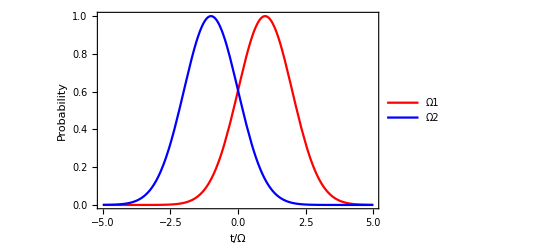

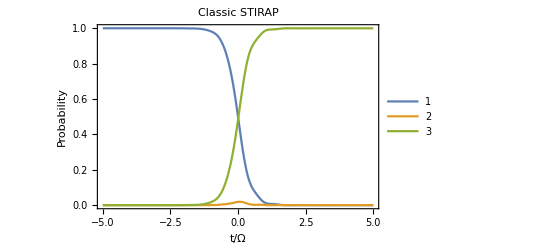

InterpolatingFunction::dmval: Input value {-4.694} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
(*Counter-intuitive pulse sequence*)
w=1;
μ=2;
Ω0=6π;
Ω1[t_]:=Ω0 Exp[(-(t-μ/2)^2)/(2 w^2)];
Ω2[t_]:=Ω0 Exp[(-(t+μ/2)^2)/(2 w^2)];
Δ1 = Δ2 = 0;
H=({{0, Ω1[t]/2, 0}, {Ω1[t]/2, Δ1, Ω2[t]/2}, {0, Ω2[t]/2, Δ1-Δ2}});
ψ0={1,0,0};(*start with atom in ground state*)
tmax=5;
(*{ψ,sys}=BuildSchroedingerSystem[H,ψ0,-tmax];
{time,soln}= Timing[First@NDSolve[sys, psi, {t,-tmax,tmax}]];*)

{ψ,sys}=BuildSchroedingerSystem[H,ψ0,-tmax];
{time,soln}= Timing[First@NDSolve[sys, ψ, {t,-tmax,tmax}]];

Print[StringForm["Time to run sim: `` mins",Floor[time/60//N]]];
soln = Table[soln[[i,2]],{i,Range[Length[soln]]}];
Plot[{Ω1[t]/Ω0,Ω2[t]/Ω0},{t,-tmax,tmax},PlotLegends->{"Ω1","Ω2"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All,PlotStyle->{Red,Blue}]
leg = {"1","2","3"};
plt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2},{t,-tmax,tmax},PlotLegends->leg,PlotLabel-> Style[StringForm["Classic STIRAP"],Black,FontSize->14],LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All]

Manipulate[TorqueVectorSphere[soln[[1]],ⅈ soln[[2]],soln[[3]],Ω2[t]/Ω0,0,-(Ω1[t]/Ω0)]/.t-> τ,{τ,-tmax,tmax,0.001} ]
```

```mathematica
(*gif =Table[TorqueVectorSphere[soln[[1]],ⅈ soln[[2]],soln[[3]],Ω2[t]/Ω0,0,Ω1[t]/Ω0]/.t-> τ,{τ,-tmax,tmax,0.2}];
Export["counter_intuitive2.gif",gif]*)
```

counter_intuitive2.gif

```mathematica
(*gif =Table[TorqueVectorSphere[soln[[1]],ⅈ soln[[2]],soln[[3]],Ω2[t]/Ω0,0,Ω1[t]/Ω0]/.t-> τ,{τ,-tmax,tmax,0.2}];
Export["intuitive1.gif",gif]*)
```

intuitive1.gif

Time to run sim: 0 mins

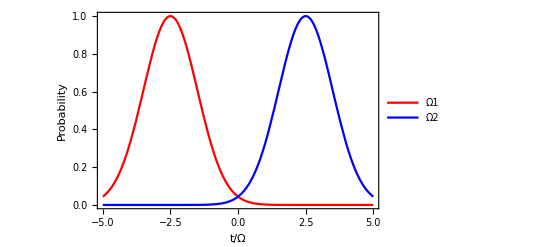

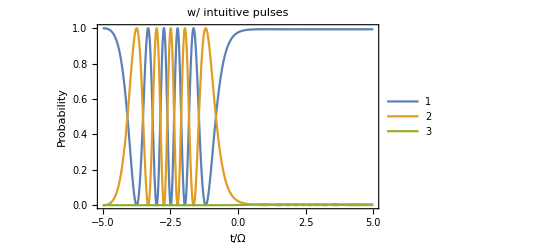

InterpolatingFunction::dmval: Input value {-5.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
(*Intuitive pulse sequence*)
w=1;
μ=5;
Ω0=4π;
Ω1[t_]:=Ω0 Exp[(-(t+μ/2)^2)/(2 w^2)];
Ω2[t_]:=Ω0 Exp[(-(t-μ/2)^2)/(2 w^2)];
Δ1 = Δ2 = 0;
H=({{0, Ω1[t]/2, 0}, {Ω1[t]/2, Δ1, Ω2[t]/2}, {0, Ω2[t]/2, Δ1-Δ2}});
ψ={1,0,0};(*start with atom in ground state*)
tmax=5;
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,-tmax];
{time,soln}= Timing[First@NDSolve[sys, ψ, {t,-tmax,tmax}]];
Print[StringForm["Time to run sim: `` mins",Floor[time/60//N]]];
soln = Table[soln[[i,2]],{i,Range[Length[soln]]}];
Plot[{Ω1[t]/Ω0,Ω2[t]/Ω0},{t,-tmax,tmax},PlotLegends->{"Ω1","Ω2"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All,PlotStyle->{Red,Blue}]
leg = {"1","2","3"};
plt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2},{t,-tmax,tmax},PlotLegends->leg,PlotLabel-> Style[StringForm["w/ intuitive pulses"],Black,FontSize->14],LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All]

Manipulate[TorqueVectorSphere[soln[[1]],ⅈ soln[[2]],soln[[3]],Ω2[t]/Ω0,0,-Ω1[t]/Ω0]/.t-> τ,{τ,-tmax,tmax,0.001} ]
```

```mathematica
(*gif =Table[TorqueVectorSphere[soln[[1]],ⅈ soln[[2]],soln[[3]],Ω2[t]/Ω0,0,Ω1[t]/Ω0]/.t-> τ,{τ,-tmax,tmax,0.2}];
Export["intuitive2.gif",gif]*)
```

intuitive2.gif

Raman

Time to run sim: 0 mins

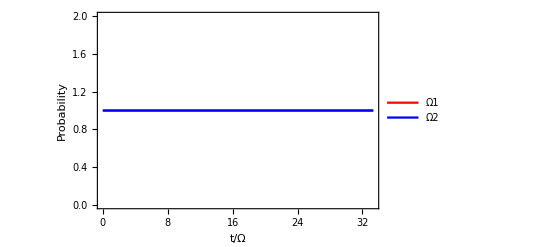

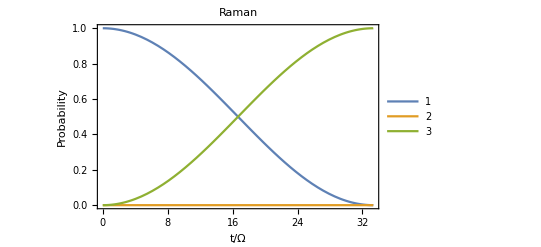

```mathematica
(*Raman pulse sequence*)
Ω0=6π;
Ω1[t_]:=Ω0 ;
Ω2[t_]:=Ω0 ;
Δ1 = Δ2 = 100Ω0;
H=({{0, Ω1[t]/2, 0}, {Ω1[t]/2, Δ1, Ω2[t]/2}, {0, Ω2[t]/2, Δ1-Δ2}});
ψ0={1,0,0};(*start with atom in ground state*)
Ωeff = Ω1[0]Ω2[0]/(2Δ1);
tmax=π/Ωeff;
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,0];
{time,soln}= Timing[First@NDSolve[sys, ψ, {t,0,tmax}]];
Print[StringForm["Time to run sim: `` mins",Floor[time/60//N]]];
soln = Table[soln[[i,2]],{i,Range[Length[soln]]}];
Plot[{Ω1[t]/Ω0,Ω2[t]/Ω0},{t,0,tmax},PlotLegends->{"Ω1","Ω2"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All,PlotStyle->{Red,Blue}]
leg = {"1","2","3"};
plt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2},{t,0,tmax},PlotLegends->leg,PlotLabel-> Style[StringForm["Raman"],Black,FontSize->14],LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All]

Manipulate[TorqueVectorSphere[Abs[soln[[1]]],Abs[soln[[2]]], Abs[ soln[[3]]],Ω2[t]/Ω0,0,-Ω1[t]/Ω0]/.t-> τ,{τ,0,tmax,0.1} ]
```

Time to run sim: 0 mins

-Graphics-

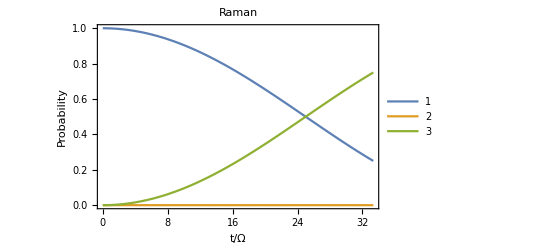

```mathematica
(*Raman pulse sequence*)
Ω0=4π;
Ω1[t_]:=Ω0 ;
Ω2[t_]:=Ω0 ;
Δ1 = Δ2 = 100Ω0;
H=({{0, Ω1[t]/2, 0}, {Ω1[t]/2, Δ1, Ω2[t]/2}, {0, Ω2[t]/2, Δ1-Δ2}});
ψ0={1,0,0};(*start with atom in ground state*)
Ωeff = Ω1[0]Ω2[0]/(2Δ1);
(*tmax=π/Ωeff;*)
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,0];
{time,soln}= Timing[First@NDSolve[sys, ψ, {t,0,tmax}]];
Print[StringForm["Time to run sim: `` mins",Floor[time/60//N]]];
soln = Table[soln[[i,2]],{i,Range[Length[soln]]}];
Plot[{Ω1[t]/Ω0,Ω2[t]/Ω0},{t,0,tmax},PlotLegends->{"Ω1","Ω2"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All,PlotStyle->{Red,Blue}]
leg = {"1","2","3"};
plt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2},{t,0,tmax},PlotLegends->leg,PlotLabel-> Style[StringForm["Raman"],Black,FontSize->14],LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All]

Manipulate[TorqueVectorSphere[Abs[soln[[1]]],Abs[soln[[2]]], Abs[ soln[[3]]],Ω2[t]/Ω0,0,-Ω1[t]/Ω0]/.t-> τ,{τ,0,tmax,0.1} ]
```

Time to run sim: 0 mins

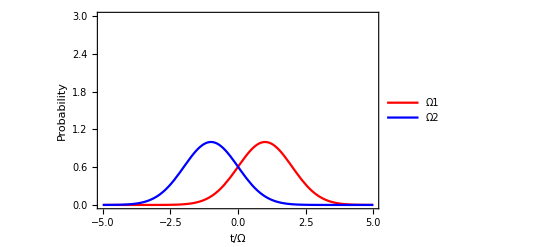

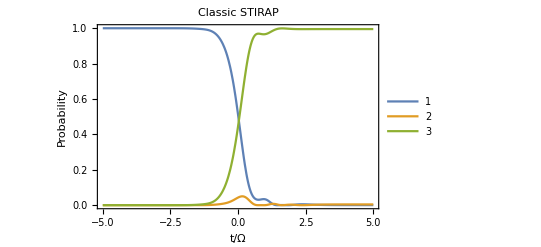

```mathematica
(*Counter-intuitive pulse sequence*)
w=1;
μ=2;
Ω0=4π;
Ω1[t_]:=Ω0 Exp[(-(t-μ/2)^2)/(2 w^2)];
Ω2[t_]:=Ω0 Exp[(-(t+μ/2)^2)/(2 w^2)];
Δ1 = Δ2 = 0;
H=({{0, Ω1[t]/2, 0}, {Ω1[t]/2, Δ1, Ω2[t]/2}, {0, Ω2[t]/2, Δ1-Δ2}});
ψ={1,0,0};(*start with atom in ground state*)
tmax=5;
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,-tmax];
{time,soln}= Timing[First@NDSolve[sys, ψ, {t,-tmax,tmax}]];
Print[StringForm["Time to run sim: `` mins",Floor[time/60//N]]];
soln = Table[soln[[i,2]],{i,Range[Length[soln]]}];
Plot[{Ω1[t]/Ω0,Ω2[t]/Ω0},{t,-tmax,tmax},PlotLegends->{"Ω1","Ω2"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->{0,3},PlotStyle->{Red,Blue}]
leg = {"1","2","3"};
plt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2},{t,-tmax,tmax},PlotLegends->leg,PlotLabel-> Style[StringForm["Classic STIRAP"],Black,FontSize->14],LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All]

Manipulate[TorqueVectorSphere[soln[[1]],ⅈ soln[[2]],soln[[3]],Ω2[t]/Ω0,0,-Ω1[t]/Ω0]/.t-> τ,{τ,-tmax,tmax,0.001} ]
```

## 4-level system

see “population transfer with delayed pulses in four-state systems”

```mathematica
(*how to choose good parameters for the pulses? seems that the peak Rabi frequency has to be just right*)
w=2;
μ=0.8;
Ω0=18;
Ωα[t_]:=Ω0 Exp[(-(t-μ/2)^2)/(2 w^2)];
Ωγ[t_]:=Ω0 Exp[(-(t+μ/2)^2)/(2 w^2)];
Ωβ[t_]:=Ω0/2;
Δ1 = Δ2 = 10;
H=({{0, Ωα[t]/2, 0, 0}, {Ωα[t]/2, Δ1, Ωβ[t]/2, 0}, {0, Ωβ[t]/2, Δ2, Ωγ[t]/2}, {0, 0, Ωγ[t]/2, 0}});
psi = {c1,c2,c3,c4};
ⅈ H.psi//MatrixForm
```

(9 ⅈ c2 ⅇ^(-1/8 (-0.4+t)^2)
ⅈ (10 c2+(9 c3)/2+9 c1 ⅇ^(-1/8 (-0.4+t)^2))
ⅈ ((9 c2)/2+10 c3+9 c4 ⅇ^(-1/8 (0.4+t)^2))
9 ⅈ c3 ⅇ^(-1/8 (0.4+t)^2))

Time to run sim: 0 mins

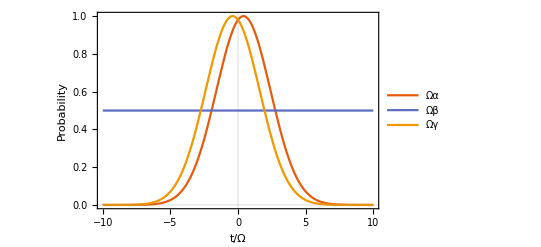

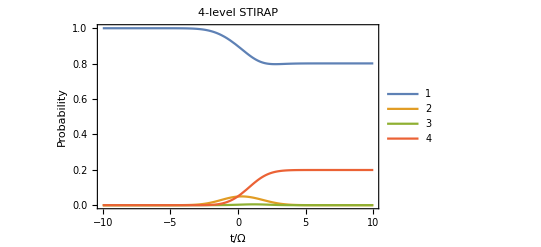

```mathematica
(*Counter-intuitive pulse sequence*)
ψ0={1,0,0,0};(*start with atom in ground state*)
tmax=10;
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,-tmax];
{time,solution}= Timing[First@NDSolve[sys, ψ, {t,-tmax,tmax}]];
Print[StringForm["Time to run sim: `` mins",Floor[time/60//N]]];
soln = Table[solution[[i,2]],{i,Range[Length[solution]]}];
Plot[{Ωα[t]/Ω0,Ωβ[t]/Ω0,Ωγ[t]/Ω0},{t,-tmax,tmax},PlotLegends->{"Ωα","Ωβ","Ωγ"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All,PlotTheme->"Scientific"]
leg = {"1","2","3","4"};
plt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2,Abs[soln[[4]]]^2},{t,-tmax,tmax},PlotLegends->leg,PlotLabel-> Style[StringForm["4-level STIRAP"],Black,FontSize->14],LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All]
```

```mathematica
(*seems like Ω=1.5Δ is about the right amount*)
Ω0list={2,1.5,1.2,1,0.7,0.5}Δ1;
soln4arr={};
ψ0={1,0,0,0};(*start with atom in ground state*)
tmax=10;
For[i=1,i<Length[Ω0list]+1,i++,
w=2;
μ=0.8;
Ω0=Ω0list[[i]];
Ωα[t_]:=Ω0 Exp[(-(t-μ/2)^2)/(2 w^2)];
Ωγ[t_]:=Ω0 Exp[(-(t+μ/2)^2)/(2 w^2)];
Ωβ[t_]:=Ω0/2;
Δ1 = Δ2 = 10;
H=({{0, Ωα[t]/2, 0, 0}, {Ωα[t]/2, Δ1, Ωβ[t]/2, 0}, {0, Ωβ[t]/2, Δ2, Ωγ[t]/2}, {0, 0, Ωγ[t]/2, 0}});
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,-tmax];
{time,solution}= Timing[First@NDSolve[sys, ψ, {t,-tmax,tmax}]];
Print[StringForm["Time to run sim: `` mins",Floor[time/60//N]]];
soln = Table[solution[[i,2]],{i,Range[Length[solution]]}];
AppendTo[soln4arr,soln[[4]]]
]
```

Time to run sim: 0 mins

Time to run sim: 0 mins

Time to run sim: 0 mins

«3 more identical outputs»

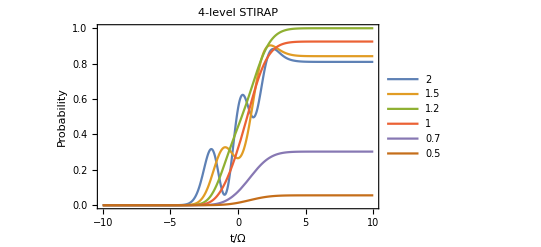

```mathematica
Plot[Evaluate[Table[Abs[soln4arr[[i]]]^2,{i,Range[Length[soln4arr]]}]],{t,-tmax,tmax},PlotLegends->Ω0list/Δ1,PlotLabel-> Style[StringForm["4-level STIRAP"],Black,FontSize->14],LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All]
```

### sensitivity to pulse details with three truncated sin^2 pulses, counterintuitive order, Δi=Ω0

Use the pulse sequences and notation of “Population transfer with delayed pulses in four-state systems”.

```mathematica
TArr={20,200};
tmin =0;
pltArr={};
For[i=1,i<Length[TArr]+1,i++,
T=TArr[[i]];
D1=0.2T;
D2=0.1T;
D3=0 T;
tmax=T+D1;
Ω0=1;(*irrelevant*)
Ωα[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D1))/T]^2,D1<=t<=T+D1}}];
Ωβ[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D2))/T]^2,D2<=t<=T+D2}}];
Ωγ[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D3))/T]^2,D3<=t<=T+D3}}];
Δ1 = Δ2 = 1;
Ωeff=Ωα[t]Ωβ[t]Ωγ[t]/(Δ1 Δ2-Ωβ[t]^2);
Δeff=(Δ1 Ωγ[t]^2-Δ2 Ωα[t]^2)/(Δ1 Δ2-Ωβ[t]^2);
(*only expected to be valid for large detuning*)

H=({{0, Ωα[t]/2, 0, 0}, {Ωα[t]/2, Δ1, Ωβ[t]/2, 0}, {0, Ωβ[t]/2, Δ2, Ωγ[t]/2}, {0, 0, Ωγ[t]/2, 0}});
(*Counter-intuitive pulse sequence*)
ψ0={1,0,0,0};(*start with atom in ground state*)
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,tmin];
{time,solution}= Timing[First@NDSolve[sys, ψ, {t,tmin,tmax}]];
Print[StringForm["Time to run sim: `` s",Floor[time//N]]];
soln = Table[solution[[i,2]],{i,Range[Length[solution]]}];
Print["T = ",TArr[[i]]];
pulseplt=Plot[{Ωα[t]/Ω0,Ωβ[t]/Ω0,Ωγ[t]/Ω0},{t,tmin,tmax},PlotLegends->{"Ωα","Ωβ","Ωγ"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Rabi frequency"},PlotRange->All,PlotTheme->"Scientific"];

detAndRabiplt=Plot[{10Ωeff,Δeff},{t,tmin,tmax},PlotLegends->{"Ωeff","Δeff"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω"},PlotRange->All,PlotTheme->"Scientific"];
leg = {"1","2","3","4"};
popplt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2,Abs[soln[[4]]]^2},{t,tmin,tmax},PlotLegends->leg,LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All];
Print[GraphicsRow[{pulseplt,popplt,detAndRabiplt},ImageSize->800]]
]
```

Time to run sim: 0 s

T = 20

-Graphics-

Time to run sim: 0 s

T = 200

-Graphics-

```mathematica
delayArr={0.1,0.5,1,3,6};
tmin =0;
pltArr={};
For[i=1,i<Length[delayArr]+1,i++,
T=200;
D1=delayArr[[i]]0.2T;
D2=delayArr[[i]]0.1T;
D3=0 T;
tmax=T+D1;
Ω0=1;(*irrelevant*)
Ωα[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D1))/T]^2,D1<=t<=T+D1}}];
Ωβ[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D2))/T]^2,D2<=t<=T+D2}}];
Ωγ[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D3))/T]^2,D3<=t<=T+D3}}];
Δ1 = Δ2 = 1;
Ωeff=Ωα[t]Ωβ[t]Ωγ[t]/(Δ1 Δ2-Ωβ[t]^2);
Δeff=(Δ1 Ωγ[t]^2-Δ2 Ωα[t]^2)/(Δ1 Δ2-Ωβ[t]^2);
(*only expected to be valid for large detuning*)

H=({{0, Ωα[t]/2, 0, 0}, {Ωα[t]/2, Δ1, Ωβ[t]/2, 0}, {0, Ωβ[t]/2, Δ2, Ωγ[t]/2}, {0, 0, Ωγ[t]/2, 0}});
(*Counter-intuitive pulse sequence*)
ψ0={1,0,0,0};(*start with atom in ground state*)
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,tmin];
{time,solution}= Timing[First@NDSolve[sys, ψ, {t,tmin,tmax}]];
Print[StringForm["Time to run sim: `` s",Floor[time//N]]];
soln = Table[solution[[i,2]],{i,Range[Length[solution]]}];
Print["delay = ",0.1delayArr[[i]]];
pulseplt=Plot[{Ωα[t]/Ω0,Ωβ[t]/Ω0,Ωγ[t]/Ω0},{t,tmin,tmax},PlotLegends->{"Ωα","Ωβ","Ωγ"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Rabi frequency"},PlotRange->All,PlotTheme->"Scientific"];

detAndRabiplt=Plot[{Ωeff,Δeff},{t,tmin,tmax},PlotLegends->{"Ωeff","Δeff"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω"},PlotRange->All,PlotTheme->"Scientific"];
leg = {"1","2","3","4"};
popplt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2,Abs[soln[[4]]]^2},{t,tmin,tmax},PlotLegends->leg,LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All];
Print[GraphicsRow[{pulseplt,popplt,detAndRabiplt},ImageSize->800]]
]
```

Time to run sim: 0 s

delay = 0.01

-Graphics-

Time to run sim: 0 s

delay = 0.05

-Graphics-

Time to run sim: 0 s

delay = 0.1

-Graphics-

Time to run sim: 0 s

delay = 0.3

-Graphics-

Time to run sim: 0 s

delay = 0.6

-Graphics-

It’s clear from the last row of plots that the absence of fields α and γ during the peak of the β pulse results in only a transient population change in the initial state before reverting to the initial state. On the opposite limit, pulses which are spaced two closely lead to Rabi oscillations between all the levels, where the final state is very sensitive to the details of the pulses.

### sensitivity to pulse details with α,γ truncated sin^2 pulses and constant β, counterintuitive order, Δi=Ω0, all Ωi equal

Use the pulse sequences and notation of “Population transfer with delayed pulses in four-state systems”.

```mathematica
TArr={20,50,200};
tmin =0;
pltArr={};
For[i=1,i<Length[TArr]+1,i++,
T=TArr[[i]];
D1=0.2T;
D2=0.1T;
D3=0 T;
tmax=T+D1;
Ω0=1;(*irrelevant*)
Ωα[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D1))/T]^2,D1<=t<=T+D1}}];
Ωβ[t_]:=2Ω0 ;
Ωγ[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D3))/T]^2,D3<=t<=T+D3}}];
Δ1 = Δ2 = 1;
Ωeff=Ωα[t]Ωβ[t]Ωγ[t]/(Δ1 Δ2-Ωβ[t]^2);
Δeff=(Δ1 Ωγ[t]^2-Δ2 Ωα[t]^2)/(Δ1 Δ2-Ωβ[t]^2);
(*only expected to be valid for large detuning*)

H=({{0, Ωα[t]/2, 0, 0}, {Ωα[t]/2, Δ1, Ωβ[t]/2, 0}, {0, Ωβ[t]/2, Δ2, Ωγ[t]/2}, {0, 0, Ωγ[t]/2, 0}});
(*Counter-intuitive pulse sequence*)
ψ0={1,0,0,0};(*start with atom in ground state*)
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,tmin];
{time,solution}= Timing[First@NDSolve[sys, ψ, {t,tmin,tmax}]];
Print[StringForm["Time to run sim: `` s",Floor[time//N]]];
soln = Table[solution[[i,2]],{i,Range[Length[solution]]}];
Print["T = ",TArr[[i]]];
pulseplt=Plot[{Ωα[t]/Ω0,Ωβ[t]/Ω0,Ωγ[t]/Ω0},{t,tmin,tmax},PlotLegends->{"Ωα","Ωβ","Ωγ"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Rabi frequency"},PlotRange->All,PlotTheme->"Scientific"];

detAndRabiplt=Plot[{10Ωeff,Δeff},{t,tmin,tmax},PlotLegends->{"Ωeff","Δeff"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω"},PlotRange->All,PlotTheme->"Scientific"];
leg = {"1","2","3","4"};
popplt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2,Abs[soln[[4]]]^2},{t,tmin,tmax},PlotLegends->leg,LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All];
Print[GraphicsRow[{pulseplt,popplt,detAndRabiplt},ImageSize->800]]
]
```

Time to run sim: 0 s

T = 20

-Graphics-

Time to run sim: 0 s

T = 50

-Graphics-

Time to run sim: 0 s

T = 200

-Graphics-

The above plots again show that the adiabatic condition is more satisfied for later times, and the oscillations on 4 get faster and smaller at longer pulse durations.

```mathematica
delayArr={0.1,0.5,1,3,6};
tmin =0;
pltArr={};
For[i=1,i<Length[delayArr]+1,i++,
T=200;
D1=delayArr[[i]]0.2T;
D2=delayArr[[i]]0.1T;
D3=0 T;
tmax=T+D1;
Ω0=1;(*irrelevant*)
Ωα[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D1))/T]^2,D1<=t<=T+D1}}];
Ωβ[t_]:=2Ω0 ;
Ωγ[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D3))/T]^2,D3<=t<=T+D3}}];
Δ1 = Δ2 = 1;
Ωeff=Ωα[t]Ωβ[t]Ωγ[t]/(Δ1 Δ2-Ωβ[t]^2);
Δeff=(Δ1 Ωγ[t]^2-Δ2 Ωα[t]^2)/(Δ1 Δ2-Ωβ[t]^2);
(*only expected to be valid for large detuning*)

H=({{0, Ωα[t]/2, 0, 0}, {Ωα[t]/2, Δ1, Ωβ[t]/2, 0}, {0, Ωβ[t]/2, Δ2, Ωγ[t]/2}, {0, 0, Ωγ[t]/2, 0}});
(*Counter-intuitive pulse sequence*)
ψ0={1,0,0,0};(*start with atom in ground state*)
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,tmin];
{time,solution}= Timing[First@NDSolve[sys, ψ, {t,tmin,tmax}]];
Print[StringForm["Time to run sim: `` s",Floor[time//N]]];
soln = Table[solution[[i,2]],{i,Range[Length[solution]]}];
Print["delay = ",0.1delayArr[[i]]];
pulseplt=Plot[{Ωα[t]/Ω0,Ωβ[t]/Ω0,Ωγ[t]/Ω0},{t,tmin,tmax},PlotLegends->{"Ωα","Ωβ","Ωγ"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Rabi frequency"},PlotRange->All,PlotTheme->"Scientific"];

detAndRabiplt=Plot[{Ωeff,Δeff},{t,tmin,tmax},PlotLegends->{"Ωeff","Δeff"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω"},PlotRange->All,PlotTheme->"Scientific"];
leg = {"1","2","3","4"};
popplt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2,Abs[soln[[4]]]^2},{t,tmin,tmax},PlotLegends->leg,LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All];
Print[GraphicsRow[{pulseplt,popplt,detAndRabiplt},ImageSize->800]]
]
```

Time to run sim: 0 s

delay = 0.01

-Graphics-

Time to run sim: 0 s

delay = 0.05

-Graphics-

Time to run sim: 0 s

delay = 0.1

-Graphics-

Time to run sim: 0 s

delay = 0.3

-Graphics-

Time to run sim: 0 s

delay = 0.6

-Graphics-

It’s clear from the last row of plots that the absence of fields α and γ during the peak of the β pulse results in only a transient population change in the initial state before reverting to the initial state. On the opposite limit, pulses which are spaced two closely lead to Rabi oscillations between all the levels, where the final state is very sensitive to the details of the pulses.

### sensitivity to pulse details with α,γ truncated sin^2 pulses and constant β, counterintuitive order, Δi=Ω0, Ωβ weak

Use the pulse sequences and notation of “Population transfer with delayed pulses in four-state systems”.

```mathematica
TArr={20,50,200};
tmin =0;
pltArr={};
For[i=1,i<Length[TArr]+1,i++,
T=TArr[[i]];
D1=0.2T;
D2=0.1T;
D3=0 T;
tmax=T+D1;
Ω0=1;(*irrelevant*)
Ωα[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D1))/T]^2,D1<=t<=T+D1}}];
Ωβ[t_]:=Ω0/10 ;
Ωγ[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D3))/T]^2,D3<=t<=T+D3}}];
Δ1 = Δ2 = 1;
Ωeff=Ωα[t]Ωβ[t]Ωγ[t]/(Δ1 Δ2-Ωβ[t]^2);
Δeff=(Δ1 Ωγ[t]^2-Δ2 Ωα[t]^2)/(Δ1 Δ2-Ωβ[t]^2);
(*only expected to be valid for large detuning*)

H=({{0, Ωα[t]/2, 0, 0}, {Ωα[t]/2, Δ1, Ωβ[t]/2, 0}, {0, Ωβ[t]/2, Δ2, Ωγ[t]/2}, {0, 0, Ωγ[t]/2, 0}});
(*Counter-intuitive pulse sequence*)
ψ0={1,0,0,0};(*start with atom in ground state*)
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,tmin];
{time,solution}= Timing[First@NDSolve[sys, ψ, {t,tmin,tmax}]];
Print[StringForm["Time to run sim: `` s",Floor[time//N]]];
soln = Table[solution[[i,2]],{i,Range[Length[solution]]}];
Print["T = ",TArr[[i]]];
pulseplt=Plot[{Ωα[t]/Ω0,Ωβ[t]/Ω0,Ωγ[t]/Ω0},{t,tmin,tmax},PlotLegends->{"Ωα","Ωβ","Ωγ"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Rabi frequency"},PlotRange->All,PlotTheme->"Scientific"];

detAndRabiplt=Plot[{10Ωeff,Δeff},{t,tmin,tmax},PlotLegends->{"Ωeff","Δeff"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω"},PlotRange->All,PlotTheme->"Scientific"];
leg = {"1","2","3","4"};
popplt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2,Abs[soln[[4]]]^2},{t,tmin,tmax},PlotLegends->leg,LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All];
Print[GraphicsRow[{pulseplt,popplt,detAndRabiplt},ImageSize->800]]
]
```

Time to run sim: 0 s

T = 20

-Graphics-

Time to run sim: 0 s

T = 50

-Graphics-

Time to run sim: 0 s

T = 200

-Graphics-

The above plots again show that the adiabatic condition is more satisfied for later times, and the oscillations on 4 get faster and smaller at longer pulse durations.

```mathematica
delayArr={0.01,.1,0.5,1,3,6};
tmin =0;
pltArr={};
For[i=1,i<Length[delayArr]+1,i++,
T=200;
D1=delayArr[[i]]0.2T;
D2=delayArr[[i]]0.1T;
D3=0 T;
tmax=T+D1;
Ω0=1;(*irrelevant*)
Ωα[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D1))/T]^2,D1<=t<=T+D1}}];
Ωβ[t_]:=Ω0/10 ;
Ωγ[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D3))/T]^2,D3<=t<=T+D3}}];
Δ1 = Δ2 = 1;
Ωeff=Ωα[t]Ωβ[t]Ωγ[t]/(Δ1 Δ2-Ωβ[t]^2);
Δeff=(Δ1 Ωγ[t]^2-Δ2 Ωα[t]^2)/(Δ1 Δ2-Ωβ[t]^2);
(*only expected to be valid for large detuning*)

H=({{0, Ωα[t]/2, 0, 0}, {Ωα[t]/2, Δ1, Ωβ[t]/2, 0}, {0, Ωβ[t]/2, Δ2, Ωγ[t]/2}, {0, 0, Ωγ[t]/2, 0}});
(*Counter-intuitive pulse sequence*)
ψ0={1,0,0,0};(*start with atom in ground state*)
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,tmin];
{time,solution}= Timing[First@NDSolve[sys, ψ, {t,tmin,tmax}]];
Print[StringForm["Time to run sim: `` s",Floor[time//N]]];
soln = Table[solution[[i,2]],{i,Range[Length[solution]]}];
Print["delay = ",0.1delayArr[[i]]];
pulseplt=Plot[{Ωα[t]/Ω0,Ωβ[t]/Ω0,Ωγ[t]/Ω0},{t,tmin,tmax},PlotLegends->{"Ωα","Ωβ","Ωγ"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Rabi frequency"},PlotRange->All,PlotTheme->"Scientific"];

detAndRabiplt=Plot[{Ωeff,Δeff},{t,tmin,tmax},PlotLegends->{"Ωeff","Δeff"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω"},PlotRange->All,PlotTheme->"Scientific"];
leg = {"1","2","3","4"};
popplt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2,Abs[soln[[4]]]^2},{t,tmin,tmax},PlotLegends->leg,LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All];
Print[GraphicsRow[{pulseplt,popplt,detAndRabiplt},ImageSize->800]]
]
```

Time to run sim: 0 s

delay = 0.001

-Graphics-

Time to run sim: 0 s

delay = 0.01

-Graphics-

Time to run sim: 0 s

delay = 0.05

-Graphics-

Time to run sim: 0 s

delay = 0.1

-Graphics-

Time to run sim: 0 s

delay = 0.3

-Graphics-

Time to run sim: 0 s

delay = 0.6

-Graphics-

For Ωβ < Ωα,γ ~Δi, there is only a transient perturbations to 1 unless the delay between α and γ is very small. Note the the first row is a tenth of the minimum delay we used in other simulations above.

### sensitivity to pulse details with α,γ truncated sin^2 pulses and constant β, counterintuitive order, Δi=10Ω0, all Ωi equal

Use the pulse sequences and notation of “Population transfer with delayed pulses in four-state systems”.

```mathematica
TArr={200,500,1000,2000,3000};
tmin =0;
pltArr={};
For[i=1,i<Length[TArr]+1,i++,
T=TArr[[i]];
D1=0.2T;
D2=0.1T;
D3=0 T;
tmax=T+D1;
Ω0=1;(*irrelevant*)
Ωα[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D1))/T]^2,D1<=t<=T+D1}}];
Ωβ[t_]:=2Ω0 ;
Ωγ[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D3))/T]^2,D3<=t<=T+D3}}];
Δ1 = Δ2 = 10Ω0;
Ωeff=Ωα[t]Ωβ[t]Ωγ[t]/(Δ1 Δ2-Ωβ[t]^2);
Δeff=(Δ1 Ωγ[t]^2-Δ2 Ωα[t]^2)/(Δ1 Δ2-Ωβ[t]^2);
(*only expected to be valid for large detuning*)

H=({{0, Ωα[t]/2, 0, 0}, {Ωα[t]/2, Δ1, Ωβ[t]/2, 0}, {0, Ωβ[t]/2, Δ2, Ωγ[t]/2}, {0, 0, Ωγ[t]/2, 0}});
(*Counter-intuitive pulse sequence*)
ψ0={1,0,0,0};(*start with atom in ground state*)
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,tmin];
{time,solution}= Timing[First@NDSolve[sys, ψ, {t,tmin,tmax}]];
Print[StringForm["Time to run sim: `` s",Floor[time//N]]];
soln = Table[solution[[i,2]],{i,Range[Length[solution]]}];
Print["T = ",TArr[[i]]];
pulseplt=Plot[{Ωα[t]/Ω0,Ωβ[t]/Ω0,Ωγ[t]/Ω0},{t,tmin,tmax},PlotLegends->{"Ωα","Ωβ","Ωγ"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Rabi frequency"},PlotRange->All,PlotTheme->"Scientific"];

detAndRabiplt=Plot[{10Ωeff,Δeff},{t,tmin,tmax},PlotLegends->{"Ωeff","Δeff"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω"},PlotRange->All,PlotTheme->"Scientific"];
leg = {"1","2","3","4"};
popplt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2,Abs[soln[[4]]]^2},{t,tmin,tmax},PlotLegends->leg,LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All];
Print[GraphicsRow[{pulseplt,popplt,detAndRabiplt},ImageSize->800]]
]
```

Time to run sim: 0 s

T = 200

-Graphics-

Time to run sim: 0 s

T = 500

-Graphics-

Time to run sim: 1 s

T = 1000

-Graphics-

Time to run sim: 1 s

T = 2000

-Graphics-

Time to run sim: 0 s

T = 3000

-Graphics-

The above plots show that very long evolution times compared to 1/Ωeff are required to acheive efficient population transfer.

```mathematica
delayArr={0.001,0.01,0.1,0.5,1};
tmin =0;
pltArr={};
For[i=1,i<Length[delayArr]+1,i++,
T=1000;
D1=delayArr[[i]]0.2T;
D2=delayArr[[i]]0.1T;
D3=0 T;
tmax=T+D1;
Ω0=1;(*irrelevant*)
Ωα[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D1))/T]^2,D1<=t<=T+D1}}];
Ωβ[t_]:=2Ω0 ;
Ωγ[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D3))/T]^2,D3<=t<=T+D3}}];
Δ1 = Δ2 = 10Ω0;
Ωeff=Ωα[t]Ωβ[t]Ωγ[t]/(Δ1 Δ2-Ωβ[t]^2);
Δeff=(Δ1 Ωγ[t]^2-Δ2 Ωα[t]^2)/(Δ1 Δ2-Ωβ[t]^2);
(*only expected to be valid for large detuning*)

H=({{0, Ωα[t]/2, 0, 0}, {Ωα[t]/2, Δ1, Ωβ[t]/2, 0}, {0, Ωβ[t]/2, Δ2, Ωγ[t]/2}, {0, 0, Ωγ[t]/2, 0}});
(*Counter-intuitive pulse sequence*)
ψ0={1,0,0,0};(*start with atom in ground state*)
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,tmin];
{time,solution}= Timing[First@NDSolve[sys, ψ, {t,tmin,tmax}]];
Print[StringForm["Time to run sim: `` s",Floor[time//N]]];
soln = Table[solution[[i,2]],{i,Range[Length[solution]]}];
Print["delay = ",0.1delayArr[[i]]];
pulseplt=Plot[{Ωα[t]/Ω0,Ωβ[t]/Ω0,Ωγ[t]/Ω0},{t,tmin,tmax},PlotLegends->{"Ωα","Ωβ","Ωγ"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Rabi frequency"},PlotRange->All,PlotTheme->"Scientific"];

detAndRabiplt=Plot[{Ωeff,Δeff},{t,tmin,tmax},PlotLegends->{"Ωeff","Δeff"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω"},PlotRange->All,PlotTheme->"Scientific"];
leg = {"1","2","3","4"};
popplt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2,Abs[soln[[4]]]^2},{t,tmin,tmax},PlotLegends->leg,LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All];
Print[GraphicsRow[{pulseplt,popplt,detAndRabiplt},ImageSize->800]]
]
```

Time to run sim: 0 s

delay = 0.0001

-Graphics-

Time to run sim: 0 s

delay = 0.001

-Graphics-

Time to run sim: 1 s

delay = 0.01

-Graphics-

Time to run sim: 0 s

delay = 0.05

-Graphics-

Time to run sim: 0 s

delay = 0.1

-Graphics-

The plots above indicate that there is a sensitive and likely imperfect maximum transfer acheived as a function of pulse delay, for T=500.

### sensitivity to pulse details with α,γ truncated sin^2 pulses and constant β, counterintuitive order, Δi=Ω0/10, all Ωi equal

Use the pulse sequences and notation of “Population transfer with delayed pulses in four-state systems”.

```mathematica
TArr={200,500,1000,2000,3000};
tmin =0;
pltArr={};
For[i=1,i<Length[TArr]+1,i++,
T=TArr[[i]];
D1=0.2T;
D2=0.1T;
D3=0 T;
tmax=T+D1;
Ω0=1;(*irrelevant*)
Ωα[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D1))/T]^2,D1<=t<=T+D1}}];
Ωβ[t_]:=2Ω0 ;
Ωγ[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D3))/T]^2,D3<=t<=T+D3}}];
Δ1 = Δ2 = 10Ω0;
Ωeff=Ωα[t]Ωβ[t]Ωγ[t]/(Δ1 Δ2-Ωβ[t]^2);
Δeff=(Δ1 Ωγ[t]^2-Δ2 Ωα[t]^2)/(Δ1 Δ2-Ωβ[t]^2);
(*only expected to be valid for large detuning*)

H=({{0, Ωα[t]/2, 0, 0}, {Ωα[t]/2, Δ1, Ωβ[t]/2, 0}, {0, Ωβ[t]/2, Δ2, Ωγ[t]/2}, {0, 0, Ωγ[t]/2, 0}});
(*Counter-intuitive pulse sequence*)
ψ0={1,0,0,0};(*start with atom in ground state*)
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,tmin];
{time,solution}= Timing[First@NDSolve[sys, ψ, {t,tmin,tmax}]];
Print[StringForm["Time to run sim: `` s",Floor[time//N]]];
soln = Table[solution[[i,2]],{i,Range[Length[solution]]}];
Print["T = ",TArr[[i]]];
pulseplt=Plot[{Ωα[t]/Ω0,Ωβ[t]/Ω0,Ωγ[t]/Ω0},{t,tmin,tmax},PlotLegends->{"Ωα","Ωβ","Ωγ"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Rabi frequency"},PlotRange->All,PlotTheme->"Scientific"];

detAndRabiplt=Plot[{10Ωeff,Δeff},{t,tmin,tmax},PlotLegends->{"Ωeff","Δeff"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω"},PlotRange->All,PlotTheme->"Scientific"];
leg = {"1","2","3","4"};
popplt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2,Abs[soln[[4]]]^2},{t,tmin,tmax},PlotLegends->leg,LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All];
Print[GraphicsRow[{pulseplt,popplt,detAndRabiplt},ImageSize->800]]
]
```

Time to run sim: 0 s

T = 200

-Graphics-

Time to run sim: 0 s

T = 500

-Graphics-

Time to run sim: 1 s

T = 1000

-Graphics-

Time to run sim: 1 s

T = 2000

-Graphics-

Time to run sim: 0 s

T = 3000

-Graphics-

The above plots show that very long evolution times compared to 1/Ωeff are required to acheive efficient population transfer.

```mathematica
delayArr={0.1,1,2,3.5,5};
tmin =0;
pltArr={};
For[i=1,i<Length[delayArr]+1,i++,
T=200;
D1=delayArr[[i]]0.2T;
D2=delayArr[[i]]0.1T;
D3=0 T;
tmax=T+D1;
Ω0=1;(*irrelevant*)
Ωα[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D1))/T]^2,D1<=t<=T+D1}}];
Ωβ[t_]:=2Ω0 ;
Ωγ[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D3))/T]^2,D3<=t<=T+D3}}];
Δ1 = Δ2 = Ω0/10;
Ωeff=Ωα[t]Ωβ[t]Ωγ[t]/(Δ1 Δ2-Ωβ[t]^2);
Δeff=(Δ1 Ωγ[t]^2-Δ2 Ωα[t]^2)/(Δ1 Δ2-Ωβ[t]^2);
(*only expected to be valid for large detuning*)

H=({{0, Ωα[t]/2, 0, 0}, {Ωα[t]/2, Δ1, Ωβ[t]/2, 0}, {0, Ωβ[t]/2, Δ2, Ωγ[t]/2}, {0, 0, Ωγ[t]/2, 0}});
(*Counter-intuitive pulse sequence*)
ψ0={1,0,0,0};(*start with atom in ground state*)
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,tmin];
{time,solution}= Timing[First@NDSolve[sys, ψ, {t,tmin,tmax}]];
Print[StringForm["Time to run sim: `` s",Floor[time//N]]];
soln = Table[solution[[i,2]],{i,Range[Length[solution]]}];
Print["delay = ",0.1delayArr[[i]]];
pulseplt=Plot[{Ωα[t]/Ω0,Ωβ[t]/Ω0,Ωγ[t]/Ω0},{t,tmin,tmax},PlotLegends->{"Ωα","Ωβ","Ωγ"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Rabi frequency"},PlotRange->All,PlotTheme->"Scientific"];

detAndRabiplt=Plot[{Ωeff,Δeff},{t,tmin,tmax},PlotLegends->{"Ωeff","Δeff"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω"},PlotRange->All,PlotTheme->"Scientific"];
leg = {"1","2","3","4"};
popplt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2,Abs[soln[[4]]]^2},{t,tmin,tmax},PlotLegends->leg,LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All];
Print[GraphicsRow[{pulseplt,popplt,detAndRabiplt},ImageSize->800]]
]
```

Time to run sim: 0 s

delay = 0.01

-Graphics-

Time to run sim: 0 s

delay = 0.1

-Graphics-

Time to run sim: 0 s

delay = 0.2

-Graphics-

Time to run sim: 0 s

delay = 0.35

-Graphics-

Time to run sim: 0 s

delay = 0.5

-Graphics-

The plots above indicate that there is a very sensitive transfer achieved as a function of pulse delay, for T=200. The transfer stops oscillating rapidly when Ωeff is no longer greater than Δeff.

### sensitivity to pulse details with α,γ truncated sin^2 pulses and constant β, counterintuitive order, Δi=Ω0/10, Ωβ weak

#### Populations vs time

Use the pulse sequences and notation of “Population transfer with delayed pulses in four-state systems”.

```mathematica
TArr={50,500,1000,2000};
tmin =0;
pltArr={};
For[i=1,i<Length[TArr]+1,i++,
T=TArr[[i]];
D1=0.2T;
D2=0.1T;
D3=0 T;
tmax=T+D1;
Ω0=1;(*irrelevant*)
Ωα[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D1))/T]^2,D1<=t<=T+D1}}];
Ωβ[t_]:=Ω0/10 ;
Ωγ[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D3))/T]^2,D3<=t<=T+D3}}];
Δ1 = Δ2 = Ω0/10;
Ωeff=Ωα[t]Ωβ[t]Ωγ[t]/(Δ1 Δ2-Ωβ[t]^2);
Δeff=(Δ1 Ωγ[t]^2-Δ2 Ωα[t]^2)/(Δ1 Δ2-Ωβ[t]^2);
(*only expected to be valid for large detuning*)

H=({{0, Ωα[t]/2, 0, 0}, {Ωα[t]/2, Δ1, Ωβ[t]/2, 0}, {0, Ωβ[t]/2, Δ2, Ωγ[t]/2}, {0, 0, Ωγ[t]/2, 0}});
(*Counter-intuitive pulse sequence*)
ψ0={1,0,0,0};(*start with atom in ground state*)
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,tmin];
{time,solution}= Timing[First@NDSolve[sys, ψ, {t,tmin,tmax}]];
Print[StringForm["Time to run sim: `` s",Floor[time//N]]];
soln = Table[solution[[i,2]],{i,Range[Length[solution]]}];
Print["T = ",TArr[[i]]];
pulseplt=Plot[{Ωα[t]/Ω0,Ωβ[t]/Ω0,Ωγ[t]/Ω0},{t,tmin,tmax},PlotLegends->{"Ωα","Ωβ","Ωγ"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Rabi frequency"},PlotRange->All,PlotTheme->"Scientific"];

detAndRabiplt=Plot[{10Ωeff,Δeff},{t,tmin,tmax},PlotLegends->{"Ωeff","Δeff"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω"},PlotRange->All,PlotTheme->"Scientific"];
leg = {"1","2","3","4"};
popplt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2,Abs[soln[[4]]]^2},{t,tmin,tmax},PlotLegends->leg,LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All];
Print[GraphicsRow[{pulseplt,popplt,detAndRabiplt},ImageSize->800]]
]
```

Power::infy: Infinite expression 1/0 encountered.

Time to run sim: 0 s

T = 50

-Graphics-

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Time to run sim: 0 s

T = 500

-Graphics-

Time to run sim: 0 s

T = 1000

-Graphics-

Time to run sim: 0 s

T = 2000

-Graphics-

```mathematica
Abs[soln[[4]]]^2/.t->tmax
```

0.850451

The above plots again show that the adiabatic condition is more satisfied for later times, and the oscillations on 4 get faster and smaller at longer pulse durations.

```mathematica
delayArr={0.01,.1,0.5,1,3,6};
tmin =0;
pltArr={};
For[i=1,i<Length[delayArr]+1,i++,
T=2000;
D1=delayArr[[i]]0.2T;
D2=delayArr[[i]]0.1T;
D3=0 T;
tmax=T+D1;
Ω0=1;(*irrelevant*)
Ωα[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D1))/T]^2,D1<=t<=T+D1}}];
Ωβ[t_]:=Ω0/10 ;
Ωγ[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D3))/T]^2,D3<=t<=T+D3}}];
Δ1 = Δ2 = Ω0/10;
Ωeff=Ωα[t]Ωβ[t]Ωγ[t]/(Δ1 Δ2-Ωβ[t]^2);
Δeff=(Δ1 Ωγ[t]^2-Δ2 Ωα[t]^2)/(Δ1 Δ2-Ωβ[t]^2);
(*only expected to be valid for large detuning*)

H=({{0, Ωα[t]/2, 0, 0}, {Ωα[t]/2, Δ1, Ωβ[t]/2, 0}, {0, Ωβ[t]/2, Δ2, Ωγ[t]/2}, {0, 0, Ωγ[t]/2, 0}});
(*Counter-intuitive pulse sequence*)
ψ0={1,0,0,0};(*start with atom in ground state*)
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,tmin];
{time,solution}= Timing[First@NDSolve[sys, ψ, {t,tmin,tmax}]];
Print[StringForm["Time to run sim: `` s",Floor[time//N]]];
soln = Table[solution[[i,2]],{i,Range[Length[solution]]}];
Print["delay = ",0.1delayArr[[i]]];
pulseplt=Plot[{Ωα[t]/Ω0,Ωβ[t]/Ω0,Ωγ[t]/Ω0},{t,tmin,tmax},PlotLegends->{"Ωα","Ωβ","Ωγ"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Rabi frequency"},PlotRange->All,PlotTheme->"Scientific"];

detAndRabiplt=Plot[{Ωeff,Δeff},{t,tmin,tmax},PlotLegends->{"Ωeff","Δeff"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω"},PlotRange->All,PlotTheme->"Scientific"];
leg = {"1","2","3","4"};
popplt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2,Abs[soln[[4]]]^2},{t,tmin,tmax},PlotLegends->leg,LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All];
Print[GraphicsRow[{pulseplt,popplt,detAndRabiplt},ImageSize->800]]
]
```

Power::infy: Infinite expression 1/0 encountered.

Time to run sim: 0 s

delay = 0.001

-Graphics-

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Time to run sim: 0 s

delay = 0.01

-Graphics-

Time to run sim: 0 s

delay = 0.05

-Graphics-

Time to run sim: 0 s

delay = 0.1

-Graphics-

Time to run sim: 0 s

delay = 0.3

-Graphics-

Time to run sim: 0 s

delay = 0.6

-Graphics-

For Ωβ < Ωα,γ <Δi, there is a sweet spot in the delay where near perfect population transfer can be acheived.

#### Population transfer vs parameters

Use the pulse sequences and notation of “Population transfer with delayed pulses in four-state systems”.

```mathematica
TArr=Range[10,2000,100](*{50,500,1000,2000}*);
delayArr=Range[0.1,5,0.1](*{0.01,.1,0.5,1,3,6}*);
tmin =0;
solnGrid=Array[0&,{Length[TArr],Length[delayArr]}];(*stores the final population in state 4 at each parameter tuple*)
(*ΔGrid=Array[0&,{Length[TArr],Length[delayArr]}];
ΩGrid=Array[0&,{Length[TArr],Length[delayArr]}];*)
totalTime=0;
For[i=1,i<Length[TArr]+1,i++,
For[j=1,j<Length[delayArr],j++,
T=TArr[[i]];
delay=delayArr[[j]];
D1=delay 0.2T;
D2=delay 0.1T;
D3=0 T;
tmax=T+D1;
Ω0=1;(*irrelevant*)
Ωα[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D1))/T]^2,D1<=t<=T+D1}}];
Ωβ[t_]:=Ω0/10 ;
Ωγ[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D3))/T]^2,D3<=t<=T+D3}}];
Δ1 = Δ2 = Ω0/10;
(*Ωeff=Ωα[t]Ωβ[t]Ωγ[t]/(Δ1 Δ2-Ωβ[t]^2);
Δeff=(Δ1 Ωγ[t]^2-Δ2 Ωα[t]^2)/(Δ1 Δ2-Ωβ[t]^2);*)
(*only expected to be valid for large detuning*)

H=({{0, Ωα[t]/2, 0, 0}, {Ωα[t]/2, Δ1, Ωβ[t]/2, 0}, {0, Ωβ[t]/2, Δ2, Ωγ[t]/2}, {0, 0, Ωγ[t]/2, 0}});
(*Counter-intuitive pulse sequence*)
ψ0={1,0,0,0};(*start with atom in ground state*)
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,tmin];
{time,solution}= Timing[First@NDSolve[sys, ψ, {t,tmin,tmax}]];
totalTime+=time;
soln = Table[solution[[i,2]],{i,Range[Length[solution]]}];
solnGrid[[i,j]]=Abs[soln[[4]]]^2/.t->tmax;
(*ΔGrid[[i,j]]=Abs[soln[[4]]]^2/.t->tmax;
ΩGrid[[i,j]]=Abs[soln[[4]]]^2/.t->tmax;*)
]
]
Print[StringForm["Time to run sim: `` s",totalTime//N]];
```

Time to run sim: 47.7969 s

```mathematica
Flatten[Table[{i,j},{i,Range[3]},{j,Range[3]}],1]
```

{{1,1},{1,2},{1,3},{2,1},{2,2},{2,3},{3,1},{3,2},{3,3}}

```mathematica
solnGridandCoords=Flatten[Table[{TArr[[i]],delayArr[[j]],solnGrid[[i,j]]},{i,Range[Length[TArr]]},{j,Range[Length[delayArr]]}],1];
```

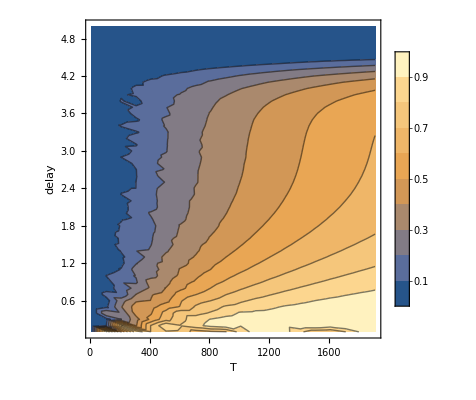

```mathematica
ListContourPlot[solnGridandCoords,LabelStyle->Directive[Black,FontSize->14],FrameLabel->{"T","delay"}, PlotLegends->Automatic,PlotRange->All]
```

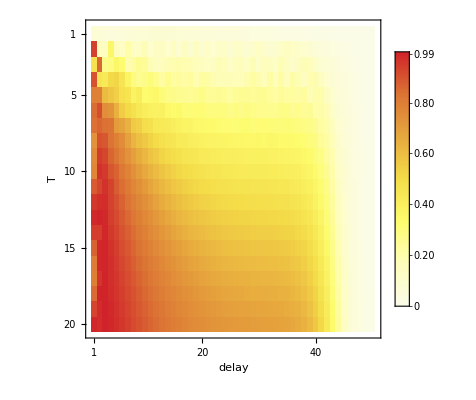

```mathematica
MatrixPlot[solnGrid,LabelStyle->Directive[Black,FontSize->14],FrameLabel->{"T","delay"}, PlotLegends->Automatic, AspectRatio->1,ColorFunction->"TemperatureMap"]
```

```mathematica
solnGrid[[20,1]]
```

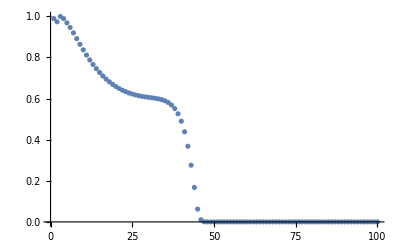

```mathematica
ListPlot[solnGrid[[20,;;]]]
```

### sensitivity to pulse details with α,γ truncated sin^2 pulses and decaying β, counterintuitive order, Δi=Ω0, Ωβ weak

#### Populations vs time

Use the pulse sequences and notation of “Population transfer with delayed pulses in four-state systems”.

```mathematica
TArr={50,500,1000,2000};
tmin =0;
pltArr={};
ψ0={1,0,0,0};
For[i=1,i<Length[TArr]+1,i++,
T=TArr[[i]];
D1=0.2T;
D2=0.1T;
D3=0 T;
tmax=T+D1;
t0=(T/π)π/2;(*Ωβ decay start time*)
Ω0=1;(*irrelevant*)
(*Counter-intuitive pulse sequence*)
Ωα[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D1))/T]^2,D1<=t<=T+D1}}];
Ωβ[t_]:=Piecewise[{{Exp[-(t-t0)/T]Ω0/10,t>=t0}}];
Ωγ[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D3))/T]^2,D3<=t<=T+D3}}];
Δ1 = Δ2 = Ω0;
Ωeff=Ωα[t]Ωβ[t]Ωγ[t]/(Δ1 Δ2-Ωβ[t]^2);
Δeff=(Δ1 Ωγ[t]^2-Δ2 Ωα[t]^2)/(Δ1 Δ2-Ωβ[t]^2);
(*only expected to be valid for large detuning*)

H=({{0, Ωα[t]/2, 0, 0}, {Ωα[t]/2, Δ1, Ωβ[t]/2, 0}, {0, Ωβ[t]/2, Δ2, Ωγ[t]/2}, {0, 0, Ωγ[t]/2, 0}});
(*start with atom in ground state*)
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,tmin];
{time,solution}= Timing[First@NDSolve[sys, ψ, {t,tmin,tmax}]];
Print[StringForm["Time to run sim: `` s",Floor[time//N]]];
soln = Table[solution[[i,2]],{i,Range[Length[solution]]}];
Print["T = ",TArr[[i]]];
pulseplt=Plot[{Ωα[t]/Ω0,Ωβ[t]/Ω0,Ωγ[t]/Ω0},{t,tmin,tmax},PlotLegends->{"Ωα","Ωβ","Ωγ"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Rabi frequency"},PlotRange->All,PlotTheme->"Scientific"];

detAndRabiplt=Plot[{10Ωeff,Δeff},{t,tmin,tmax},PlotLegends->{"Ωeff","Δeff"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω"},PlotRange->All,PlotTheme->"Scientific"];
leg = {"1","2","3","4"};
popplt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2,Abs[soln[[4]]]^2},{t,tmin,tmax},PlotLegends->leg,LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All];
Print[GraphicsRow[{pulseplt,popplt,detAndRabiplt},ImageSize->800]]
]
```

Time to run sim: 0 s

T = 50

-Graphics-

Time to run sim: 0 s

T = 500

-Graphics-

Time to run sim: 0 s

T = 1000

-Graphics-

Time to run sim: 0 s

T = 2000

-Graphics-

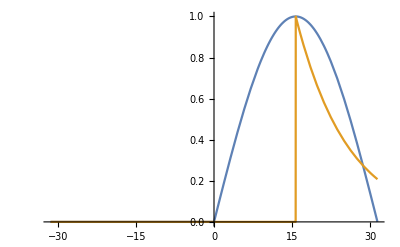

```mathematica
t0=10π/2;
Plot[{Piecewise[{{Sin[t/10],0<=t<=10π}}],Piecewise[{{Exp[-(t-t0)/10],t>t0}}]},{t,-10π,10π},PlotRange->{0,1}]
```

The above plots again show that the adiabatic condition is more satisfied for later times, and the oscillations on 4 get faster and smaller at longer pulse durations.

```mathematica
delayArr={0.01,.1,0.5,1,3,6};
tmin =0;
pltArr={};
For[i=1,i<Length[delayArr]+1,i++,
T=2000;
D1=delayArr[[i]]0.2T;
D2=delayArr[[i]]0.1T;
D3=0 T;
tmax=T+D1;
t0=(T/π)π/2;(*Ωβ decay start time*)
Ω0=1;(*irrelevant*)
Ωα[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D1))/T]^2,D1<=t<=T+D1}}];
Ωβ[t_]:=Piecewise[{{Exp[-(t-t0)/T]Ω0/10,t>=t0}}];
Ωγ[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D3))/T]^2,D3<=t<=T+D3}}];
Δ1 = Δ2 = Ω0;
Ωeff=Ωα[t]Ωβ[t]Ωγ[t]/(Δ1 Δ2-Ωβ[t]^2);
Δeff=(Δ1 Ωγ[t]^2-Δ2 Ωα[t]^2)/(Δ1 Δ2-Ωβ[t]^2);
(*only expected to be valid for large detuning*)

H=({{0, Ωα[t]/2, 0, 0}, {Ωα[t]/2, Δ1, Ωβ[t]/2, 0}, {0, Ωβ[t]/2, Δ2, Ωγ[t]/2}, {0, 0, Ωγ[t]/2, 0}});
(*Counter-intuitive pulse sequence*)
ψ0={1,0,0,0};(*start with atom in ground state*)
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,tmin];
{time,solution}= Timing[First@NDSolve[sys, ψ, {t,tmin,tmax}]];
Print[StringForm["Time to run sim: `` s",Floor[time//N]]];
soln = Table[solution[[i,2]],{i,Range[Length[solution]]}];
Print["delay = ",0.1delayArr[[i]]];
pulseplt=Plot[{Ωα[t]/Ω0,Ωβ[t]/Ω0,Ωγ[t]/Ω0},{t,tmin,tmax},PlotLegends->{"Ωα","Ωβ","Ωγ"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Rabi frequency"},PlotRange->All,PlotTheme->"Scientific"];

detAndRabiplt=Plot[{Ωeff,Δeff},{t,tmin,tmax},PlotLegends->{"Ωeff","Δeff"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω"},PlotRange->All,PlotTheme->"Scientific"];
leg = {"1","2","3","4"};
popplt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2,Abs[soln[[4]]]^2},{t,tmin,tmax},PlotLegends->leg,LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All];
Print[GraphicsRow[{pulseplt,popplt,detAndRabiplt},ImageSize->800]]
]
```

Time to run sim: 0 s

delay = 0.001

-Graphics-

Time to run sim: 0 s

delay = 0.01

-Graphics-

Time to run sim: 0 s

delay = 0.05

-Graphics-

Time to run sim: 0 s

delay = 0.1

-Graphics-

Time to run sim: 0 s

delay = 0.3

-Graphics-

Time to run sim: 0 s

delay = 0.6

-Graphics-

For Ωβ < Ωα,γ <Δi, there is a sweet spot in the delay where near perfect population transfer can be acheived.

#### Population transfer vs parameters

Use the pulse sequences and notation of “Population transfer with delayed pulses in four-state systems”.

```mathematica
TArr=Range[10,2000,100];
delayArr=Range[0.1,5,0.1];
tmin =0;
solnGrid=Array[0&,{Length[TArr],Length[delayArr]}];(*stores the final population in state 4 at each parameter tuple*)
(*ΔGrid=Array[0&,{Length[TArr],Length[delayArr]}];
ΩGrid=Array[0&,{Length[TArr],Length[delayArr]}];*)
totalTime=0;
For[i=1,i<Length[TArr]+1,i++,
For[j=1,j<Length[delayArr],j++,
T=TArr[[i]];
delay=delayArr[[j]];
D1=delay 0.2T;
D2=delay 0.1T;
D3=0 T;
tmax=T+D1;
t0=(T/π)π/2;(*Ωβ decay start time*)
Ω0=1;(*irrelevant*)
Ωα[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D1))/T]^2,D1<=t<=T+D1}}];
Ωβ[t_]:=Piecewise[{{Exp[-(t-t0)/T]Ω0/10,t>=t0}}];
Ωγ[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D3))/T]^2,D3<=t<=T+D3}}];
Δ1 = Δ2 = Ω0;
(*Ωeff=Ωα[t]Ωβ[t]Ωγ[t]/(Δ1 Δ2-Ωβ[t]^2);
Δeff=(Δ1 Ωγ[t]^2-Δ2 Ωα[t]^2)/(Δ1 Δ2-Ωβ[t]^2);*)
(*only expected to be valid for large detuning*)

H=({{0, Ωα[t]/2, 0, 0}, {Ωα[t]/2, Δ1, Ωβ[t]/2, 0}, {0, Ωβ[t]/2, Δ2, Ωγ[t]/2}, {0, 0, Ωγ[t]/2, 0}});
(*Counter-intuitive pulse sequence*)
ψ0={1,0,0,0};(*start with atom in ground state*)
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,tmin];
{time,solution}= Timing[First@NDSolve[sys, ψ, {t,tmin,tmax}]];
totalTime+=time;
soln = Table[solution[[i,2]],{i,Range[Length[solution]]}];
solnGrid[[i,j]]=Abs[soln[[4]]]^2/.t->tmax;
(*ΔGrid[[i,j]]=Abs[soln[[4]]]^2/.t->tmax;
ΩGrid[[i,j]]=Abs[soln[[4]]]^2/.t->tmax;*)
]
]
Print[StringForm["Time to run sim: `` s",totalTime//N]];
```

Time to run sim: 237.5 s

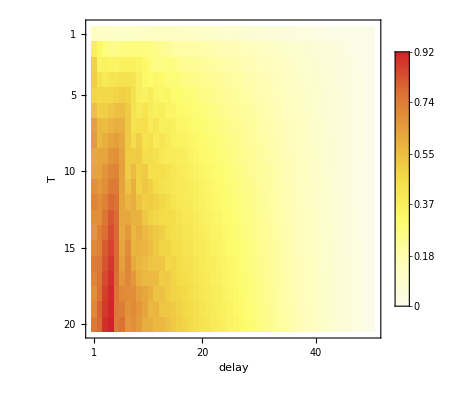

```mathematica
MatrixPlot[solnGrid,LabelStyle->Directive[Black,FontSize->14],FrameLabel->{"T","delay"}, PlotLegends->Automatic, AspectRatio->1,ColorFunction->"TemperatureMap"]
```

Todo: find out how to put custom axes on a MatrixPlot. Or cave and use ContourPlot

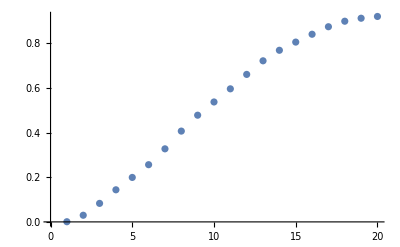

```mathematica
ListPlot[solnGrid[[;;,4]]]
```

### sensitivity to pulse details with α,γ truncated sin^2 pulses and decaying β, counterintuitive order, Δi=10*Ω0, Ωβ weak

#### Populations vs time

Use the pulse sequences and notation of “Population transfer with delayed pulses in four-state systems”.

```mathematica
TArr={50,500,1000,2000};
tmin =0;
pltArr={};
For[i=1,i<Length[TArr]+1,i++,
T=TArr[[i]];
D1=0.2T;
D2=0.1T;
D3=0 T;
tmax=T+D1;
t0=(T/π)π/2;(*Ωβ decay start time*)
Ω0=1;(*irrelevant*)
Ωα[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D1))/T]^2,D1<=t<=T+D1}}];
Ωβ[t_]:=Piecewise[{{Exp[-(t-t0)/T]Ω0/10,t>=t0}}];
Ωγ[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D3))/T]^2,D3<=t<=T+D3}}];
Δ1 = Δ2 = 10Ω0;
Ωeff=Ωα[t]Ωβ[t]Ωγ[t]/(Δ1 Δ2-Ωβ[t]^2);
Δeff=(Δ1 Ωγ[t]^2-Δ2 Ωα[t]^2)/(Δ1 Δ2-Ωβ[t]^2);
(*only expected to be valid for large detuning*)

H=({{0, Ωα[t]/2, 0, 0}, {Ωα[t]/2, Δ1, Ωβ[t]/2, 0}, {0, Ωβ[t]/2, Δ2, Ωγ[t]/2}, {0, 0, Ωγ[t]/2, 0}});
(*Counter-intuitive pulse sequence*)
ψ0={1,0,0,0};(*start with atom in ground state*)
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,tmin];
{time,solution}= Timing[First@NDSolve[sys, ψ, {t,tmin,tmax}]];
Print[StringForm["Time to run sim: `` s",Floor[time//N]]];
soln = Table[solution[[i,2]],{i,Range[Length[solution]]}];
Print["T = ",TArr[[i]]];
pulseplt=Plot[{Ωα[t]/Ω0,Ωβ[t]/Ω0,Ωγ[t]/Ω0},{t,tmin,tmax},PlotLegends->{"Ωα","Ωβ","Ωγ"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Rabi frequency"},PlotRange->All,PlotTheme->"Scientific"];

detAndRabiplt=Plot[{10Ωeff,Δeff},{t,tmin,tmax},PlotLegends->{"Ωeff","Δeff"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω"},PlotRange->All,PlotTheme->"Scientific"];
leg = {"1","2","3","4"};
popplt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2,Abs[soln[[4]]]^2},{t,tmin,tmax},PlotLegends->leg,LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All];
Print[GraphicsRow[{pulseplt,popplt,detAndRabiplt},ImageSize->800]]
]
```

Time to run sim: 0 s

T = 50

-Graphics-

Time to run sim: 0 s

T = 500

-Graphics-

Time to run sim: 0 s

T = 1000

-Graphics-

Time to run sim: 1 s

T = 2000

-Graphics-

```mathematica
t0=10π/2;
Plot[{Piecewise[{{Sin[t/10],0<=t<=10π}}],Piecewise[{{Exp[-(t-t0)/10],t>t0}}]},{t,-10π,10π},PlotRange->{0,1}]
```

-Graphics-

The above plots again show that the adiabatic condition is more satisfied for later times, and the oscillations on 4 get faster and smaller at longer pulse durations.

```mathematica
delayArr={0.01,.1,0.5,1,3,6};
tmin =0;
pltArr={};
For[i=1,i<Length[delayArr]+1,i++,
T=2000;
D1=delayArr[[i]]0.2T;
D2=delayArr[[i]]0.1T;
D3=0 T;
tmax=T+D1;
t0=(T/π)π/2;(*Ωβ decay start time*)
Ω0=1;(*irrelevant*)
Ωα[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D1))/T]^2,D1<=t<=T+D1}}];
Ωβ[t_]:=Piecewise[{{Exp[-(t-t0)/T]Ω0/10,t>=t0}}];
Ωγ[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D3))/T]^2,D3<=t<=T+D3}}];
Δ1 = Δ2 = 10Ω0;
Ωeff=Ωα[t]Ωβ[t]Ωγ[t]/(Δ1 Δ2-Ωβ[t]^2);
Δeff=(Δ1 Ωγ[t]^2-Δ2 Ωα[t]^2)/(Δ1 Δ2-Ωβ[t]^2);
(*only expected to be valid for large detuning*)

H=({{0, Ωα[t]/2, 0, 0}, {Ωα[t]/2, Δ1, Ωβ[t]/2, 0}, {0, Ωβ[t]/2, Δ2, Ωγ[t]/2}, {0, 0, Ωγ[t]/2, 0}});
(*Counter-intuitive pulse sequence*)
ψ0={1,0,0,0};(*start with atom in ground state*)
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,tmin];
{time,solution}= Timing[First@NDSolve[sys, ψ, {t,tmin,tmax}]];
Print[StringForm["Time to run sim: `` s",Floor[time//N]]];
soln = Table[solution[[i,2]],{i,Range[Length[solution]]}];
Print["delay = ",0.1delayArr[[i]]];
pulseplt=Plot[{Ωα[t]/Ω0,Ωβ[t]/Ω0,Ωγ[t]/Ω0},{t,tmin,tmax},PlotLegends->{"Ωα","Ωβ","Ωγ"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Rabi frequency"},PlotRange->All,PlotTheme->"Scientific"];

detAndRabiplt=Plot[{Ωeff,Δeff},{t,tmin,tmax},PlotLegends->{"Ωeff","Δeff"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω"},PlotRange->All,PlotTheme->"Scientific"];
leg = {"1","2","3","4"};
popplt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2,Abs[soln[[4]]]^2},{t,tmin,tmax},PlotLegends->leg,LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All];
Print[GraphicsRow[{pulseplt,popplt,detAndRabiplt},ImageSize->800]]
]
```

Time to run sim: 1 s

delay = 0.001

-Graphics-

Time to run sim: 1 s

delay = 0.01

-Graphics-

Time to run sim: 1 s

delay = 0.05

-Graphics-

Time to run sim: 1 s

delay = 0.1

-Graphics-

Time to run sim: 1 s

delay = 0.3

-Graphics-

Time to run sim: 1 s

delay = 0.6

-Graphics-

For Ωβ < Ωα,γ <Δi, there is a sweet spot in the delay where near perfect population transfer can be acheived.

#### Population transfer vs parameters

Use the pulse sequences and notation of “Population transfer with delayed pulses in four-state systems”.

```mathematica
TArr=Range[10,2000,100];
delayArr=Range[0.1,5,0.1];
tmin =0;
solnGrid=Array[0&,{Length[TArr],Length[delayArr]}];(*stores the final population in state 4 at each parameter tuple*)
(*ΔGrid=Array[0&,{Length[TArr],Length[delayArr]}];
ΩGrid=Array[0&,{Length[TArr],Length[delayArr]}];*)
totalTime=0;
For[i=1,i<Length[TArr]+1,i++,
For[j=1,j<Length[delayArr],j++,
T=TArr[[i]];
delay=delayArr[[j]];
D1=delay 0.2T;
D2=delay 0.1T;
D3=0 T;
tmax=T+D1;
t0=(T/π)π/2;(*Ωβ decay start time*)
Ω0=1;(*irrelevant*)
Ωα[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D1))/T]^2,D1<=t<=T+D1}}];
Ωβ[t_]:=Piecewise[{{Exp[-(t-t0)/T]Ω0/10,t>=t0}}];
Ωγ[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D3))/T]^2,D3<=t<=T+D3}}];
Δ1 = Δ2 = 10Ω0;
(*Ωeff=Ωα[t]Ωβ[t]Ωγ[t]/(Δ1 Δ2-Ωβ[t]^2);
Δeff=(Δ1 Ωγ[t]^2-Δ2 Ωα[t]^2)/(Δ1 Δ2-Ωβ[t]^2);*)
(*only expected to be valid for large detuning*)

H=({{0, Ωα[t]/2, 0, 0}, {Ωα[t]/2, Δ1, Ωβ[t]/2, 0}, {0, Ωβ[t]/2, Δ2, Ωγ[t]/2}, {0, 0, Ωγ[t]/2, 0}});
(*Counter-intuitive pulse sequence*)
ψ0={1,0,0,0};(*start with atom in ground state*)
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,tmin];
{time,solution}= Timing[First@NDSolve[sys, ψ, {t,tmin,tmax}]];
totalTime+=time;
soln = Table[solution[[i,2]],{i,Range[Length[solution]]}];
solnGrid[[i,j]]=Abs[soln[[4]]]^2/.t->tmax;
(*ΔGrid[[i,j]]=Abs[soln[[4]]]^2/.t->tmax;
ΩGrid[[i,j]]=Abs[soln[[4]]]^2/.t->tmax;*)
]
]
Print[StringForm["Time to run sim: `` s",totalTime//N]];
```

Time to run sim: 60.0156 s

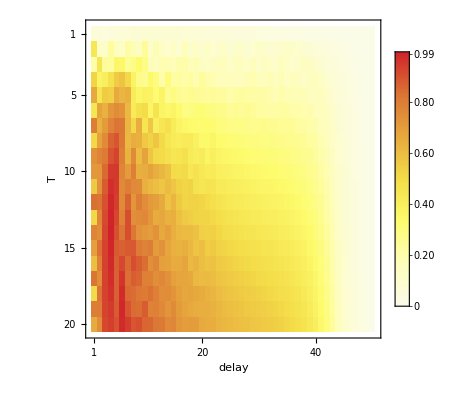

```mathematica
MatrixPlot[solnGrid,LabelStyle->Directive[Black,FontSize->14],FrameLabel->{"T","delay"}, PlotLegends->Automatic, AspectRatio->1,ColorFunction->"TemperatureMap"]
```

Todo: find out how to put custom axes on a MatrixPlot. Or cave and use ContourPlot

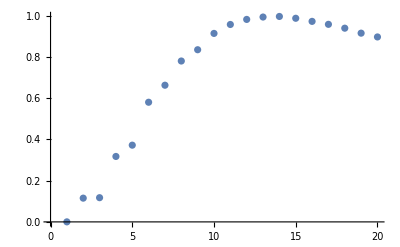

```mathematica
ListPlot[solnGrid[[;;,4]]]
```

### sensitivity to pulse details with α,γ truncated sin^2 pulses and decaying β, counterintuitive order, Δi=10*Ω0, Ωβ weak

#### Populations vs time

Use the pulse sequences and notation of “Population transfer with delayed pulses in four-state systems”.

```mathematica
TArr={50,500,1000,2000};
tmin =0;
pltArr={};
For[i=1,i<Length[TArr]+1,i++,
T=TArr[[i]];
D1=0.2T;
D2=0.1T;
D3=0 T;
tmax=T+D1;
t0=(T/π)π/2;(*Ωβ decay start time*)
Ω0=1;(*irrelevant*)
Ωα[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D1))/T]^2,D1<=t<=T+D1}}];
Ωβ[t_]:=Piecewise[{{Exp[-(t-t0)/T]Ω0/10,t>=t0}}];
Ωγ[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D3))/T]^2,D3<=t<=T+D3}}];
Δ1 = Δ2 = 10Ω0;
Ωeff=Ωα[t]Ωβ[t]Ωγ[t]/(Δ1 Δ2-Ωβ[t]^2);
Δeff=(Δ1 Ωγ[t]^2-Δ2 Ωα[t]^2)/(Δ1 Δ2-Ωβ[t]^2);
(*only expected to be valid for large detuning*)

H=({{0, Ωα[t]/2, 0, 0}, {Ωα[t]/2, Δ1, Ωβ[t]/2, 0}, {0, Ωβ[t]/2, Δ2, Ωγ[t]/2}, {0, 0, Ωγ[t]/2, 0}});
(*Counter-intuitive pulse sequence*)
ψ0={1,0,0,0};(*start with atom in ground state*)
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,tmin];
{time,solution}= Timing[First@NDSolve[sys, ψ, {t,tmin,tmax}]];
Print[StringForm["Time to run sim: `` s",Floor[time//N]]];
soln = Table[solution[[i,2]],{i,Range[Length[solution]]}];
Print["T = ",TArr[[i]]];
pulseplt=Plot[{Ωα[t]/Ω0,Ωβ[t]/Ω0,Ωγ[t]/Ω0},{t,tmin,tmax},PlotLegends->{"Ωα","Ωβ","Ωγ"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Rabi frequency"},PlotRange->All,PlotTheme->"Scientific"];

detAndRabiplt=Plot[{10Ωeff,Δeff},{t,tmin,tmax},PlotLegends->{"Ωeff","Δeff"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω"},PlotRange->All,PlotTheme->"Scientific"];
leg = {"1","2","3","4"};
popplt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2,Abs[soln[[4]]]^2},{t,tmin,tmax},PlotLegends->leg,LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All];
Print[GraphicsRow[{pulseplt,popplt,detAndRabiplt},ImageSize->800]]
]
```

Time to run sim: 0 s

T = 50

-Graphics-

Time to run sim: 0 s

T = 500

-Graphics-

Time to run sim: 0 s

T = 1000

-Graphics-

Time to run sim: 1 s

T = 2000

-Graphics-

```mathematica
t0=10π/2;
Plot[{Piecewise[{{Sin[t/10],0<=t<=10π}}],Piecewise[{{Exp[-(t-t0)/10],t>t0}}]},{t,-10π,10π},PlotRange->{0,1}]
```

-Graphics-

The above plots again show that the adiabatic condition is more satisfied for later times, and the oscillations on 4 get faster and smaller at longer pulse durations.

```mathematica
delayArr={0.01,.1,0.5,1,3,6};
tmin =0;
pltArr={};
For[i=1,i<Length[delayArr]+1,i++,
T=2000;
D1=delayArr[[i]]0.2T;
D2=delayArr[[i]]0.1T;
D3=0 T;
tmax=T+D1;
t0=(T/π)π/2;(*Ωβ decay start time*)
Ω0=1;(*irrelevant*)
Ωα[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D1))/T]^2,D1<=t<=T+D1}}];
Ωβ[t_]:=Piecewise[{{Exp[-(t-t0)/T]Ω0/10,t>=t0}}];
Ωγ[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D3))/T]^2,D3<=t<=T+D3}}];
Δ1 = Δ2 = 10Ω0;
Ωeff=Ωα[t]Ωβ[t]Ωγ[t]/(Δ1 Δ2-Ωβ[t]^2);
Δeff=(Δ1 Ωγ[t]^2-Δ2 Ωα[t]^2)/(Δ1 Δ2-Ωβ[t]^2);
(*only expected to be valid for large detuning*)

H=({{0, Ωα[t]/2, 0, 0}, {Ωα[t]/2, Δ1, Ωβ[t]/2, 0}, {0, Ωβ[t]/2, Δ2, Ωγ[t]/2}, {0, 0, Ωγ[t]/2, 0}});
(*Counter-intuitive pulse sequence*)
ψ0={1,0,0,0};(*start with atom in ground state*)
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,tmin];
{time,solution}= Timing[First@NDSolve[sys, ψ, {t,tmin,tmax}]];
Print[StringForm["Time to run sim: `` s",Floor[time//N]]];
soln = Table[solution[[i,2]],{i,Range[Length[solution]]}];
Print["delay = ",0.1delayArr[[i]]];
pulseplt=Plot[{Ωα[t]/Ω0,Ωβ[t]/Ω0,Ωγ[t]/Ω0},{t,tmin,tmax},PlotLegends->{"Ωα","Ωβ","Ωγ"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Rabi frequency"},PlotRange->All,PlotTheme->"Scientific"];

detAndRabiplt=Plot[{Ωeff,Δeff},{t,tmin,tmax},PlotLegends->{"Ωeff","Δeff"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω"},PlotRange->All,PlotTheme->"Scientific"];
leg = {"1","2","3","4"};
popplt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2,Abs[soln[[4]]]^2},{t,tmin,tmax},PlotLegends->leg,LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All];
Print[GraphicsRow[{pulseplt,popplt,detAndRabiplt},ImageSize->800]]
]
```

Time to run sim: 1 s

delay = 0.001

-Graphics-

Time to run sim: 1 s

delay = 0.01

-Graphics-

Time to run sim: 1 s

delay = 0.05

-Graphics-

Time to run sim: 1 s

delay = 0.1

-Graphics-

Time to run sim: 1 s

delay = 0.3

-Graphics-

Time to run sim: 1 s

delay = 0.6

-Graphics-

For Ωβ < Ωα,γ <Δi, there is a sweet spot in the delay where near perfect population transfer can be acheived.

#### Population transfer vs parameters

Use the pulse sequences and notation of “Population transfer with delayed pulses in four-state systems”.

```mathematica
TArr=Range[10,2000,100];
delayArr=Range[0.1,5,0.1];
tmin =0;
solnGrid=Array[0&,{Length[TArr],Length[delayArr]}];(*stores the final population in state 4 at each parameter tuple*)
(*ΔGrid=Array[0&,{Length[TArr],Length[delayArr]}];
ΩGrid=Array[0&,{Length[TArr],Length[delayArr]}];*)
totalTime=0;
For[i=1,i<Length[TArr]+1,i++,
For[j=1,j<Length[delayArr],j++,
T=TArr[[i]];
delay=delayArr[[j]];
D1=delay 0.2T;
D2=delay 0.1T;
D3=0 T;
tmax=T+D1;
t0=(T/π)π/2;(*Ωβ decay start time*)
Ω0=1;(*irrelevant*)
Ωα[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D1))/T]^2,D1<=t<=T+D1}}];
Ωβ[t_]:=Piecewise[{{Exp[-(t-t0)/T]Ω0/10,t>=t0}}];
Ωγ[t_]:=2Piecewise[{{Ω0 Sin[(π(t-D3))/T]^2,D3<=t<=T+D3}}];
Δ1 = Δ2 = 10Ω0;
(*Ωeff=Ωα[t]Ωβ[t]Ωγ[t]/(Δ1 Δ2-Ωβ[t]^2);
Δeff=(Δ1 Ωγ[t]^2-Δ2 Ωα[t]^2)/(Δ1 Δ2-Ωβ[t]^2);*)
(*only expected to be valid for large detuning*)

H=({{0, Ωα[t]/2, 0, 0}, {Ωα[t]/2, Δ1, Ωβ[t]/2, 0}, {0, Ωβ[t]/2, Δ2, Ωγ[t]/2}, {0, 0, Ωγ[t]/2, 0}});
(*Counter-intuitive pulse sequence*)
ψ0={1,0,0,0};(*start with atom in ground state*)
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,tmin];
{time,solution}= Timing[First@NDSolve[sys, ψ, {t,tmin,tmax}]];
totalTime+=time;
soln = Table[solution[[i,2]],{i,Range[Length[solution]]}];
solnGrid[[i,j]]=Abs[soln[[4]]]^2/.t->tmax;
(*ΔGrid[[i,j]]=Abs[soln[[4]]]^2/.t->tmax;
ΩGrid[[i,j]]=Abs[soln[[4]]]^2/.t->tmax;*)
]
]
Print[StringForm["Time to run sim: `` s",totalTime//N]];
```

Time to run sim: 1101.48 s

```mathematica
MatrixPlot[solnGrid,LabelStyle->Directive[Black,FontSize->14],FrameLabel->{"T","delay"}, PlotLegends->Automatic, AspectRatio->1,ColorFunction->"TemperatureMap"]
```

-Graphics-

Todo: find out how to put custom axes on a MatrixPlot. Or cave and use ContourPlot

```mathematica
ListPlot[solnGrid[[;;,4]]]
```

-Graphics-

## misc graphics

Time to run sim: 0 mins

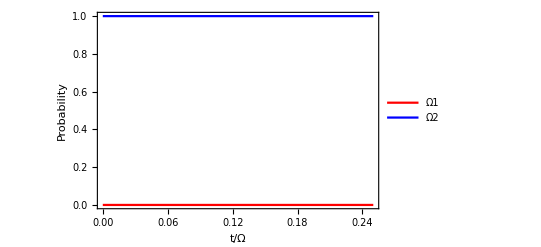

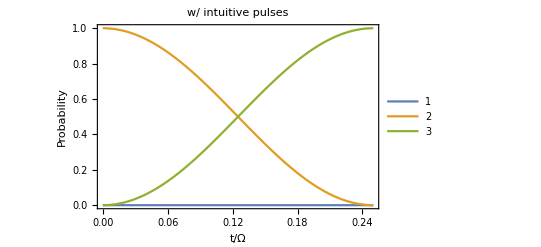

Part::partd: Part specification soln⟦1⟧ is longer than depth of object.

Part::partd: Part specification soln⟦2⟧ is longer than depth of object.

Part::partd: Part specification soln⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
(*Intuitive pulse sequence*)
w=1;
μ=5;
Ω0=4π;
Ω1[t_]:=0 ;
Ω2[t_]:=Ω0 ;
Δ1 = Δ2 = 0;
H=({{0, Ω1[t]/2, 0}, {Ω1[t]/2, Δ1, Ω2[t]/2}, {0, Ω2[t]/2, Δ1-Δ2}});
ψ0={0,-ⅈ,0};(*start with atom in ground state*)
tmax=π/Ω0;
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,0];
{time,soln}= Timing[First@NDSolve[sys, ψ, {t,0,tmax}]];
Print[StringForm["Time to run sim: `` mins",Floor[time/60//N]]];
soln = Table[soln[[i,2]],{i,Range[Length[soln]]}];
Plot[{Ω1[t]/Ω0,Ω2[t]/Ω0},{t,0,tmax},PlotLegends->{"Ω1","Ω2"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All,PlotStyle->{Red,Blue}]
leg = {"1","2","3"};
plt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2},{t,0,tmax},PlotLegends->leg,PlotLabel-> Style[StringForm["w/ intuitive pulses"],Black,FontSize->14],LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All]

Manipulate[TorqueVectorSphere[soln[[1]],ⅈ soln[[2]],soln[[3]],Ω2[t]/Ω0,0,-Ω1[t]/Ω0]/.t-> τ,{τ,0,tmax,0.001} ]
```

```mathematica
plt=Show[Table[TorqueVectorSphere[soln[[1]],ⅈ soln[[2]],soln[[3]],Ω2[t]/Ω0,0,-Ω1[t]/Ω0]/.t-> τ,{τ,0,tmax,tmax/10} ],ImageResolution-> 400]
```

-Graphics3D-

```mathematica
Export[]
```

## algebra

### derive STIRAP condition for 3 level system

I’ve assumed that the two-photon detuning Δ1-Δ2 is zero.

```mathematica
Clear[Ω1,Ω2,Δ1,Δ2]
H=({{0, Ω1/2, 0}, {Ω1/2, Δ1, Ω2/2}, {0, Ω2/2, 0}});
Assuming[{Ω1,Ω2,Δ1}∈Reals,Eigensystem[H]]
```

{{0,1/2 (Δ1-√(Δ1^2+Ω1^2+Ω2^2)),1/2 (Δ1+√(Δ1^2+Ω1^2+Ω2^2))},{{-Ω2/Ω1,0,1},{Ω1/Ω2,-(-Δ1+√(Δ1^2+Ω1^2+Ω2^2))/Ω2,1},{Ω1/Ω2,-(-Δ1-√(Δ1^2+Ω1^2+Ω2^2))/Ω2,1}}}

Clearly, the dark state is {-Ω2/Ω1,0,1} up to a normalization factor.

```mathematica
Dot[1/(√((Ω2/Ω1)^2+1)){-Ω2/Ω1,0,1},1/(√((Ω2/Ω1)^2+1)){-Ω2/Ω1,0,1}]//FullSimplify
```

1

Parametrizing the Rabi frequencies as Ω2 = cos(ϕ) and Ω1 = sin(ϕ), where ϕ is called the mixing angle, we have the dark state

D=-cos(ϕ)1+sin(ϕ)3

The initial condition that the system starts in 1 implies that Ω2 alone must be on first. this can be seen in terms of the mixing angle ϕ = arctan(Ω1/Ω2), where Ω1 must be 0 initially. 

For adiabatic following of D as ϕ is varied from 0 to π/2, we have the condition |dϕ/dt| << |Ω_eff|, where Ω_eff = √(Ω_1^2+Ω_2^2).

```mathematica
dϕ/dt=d/dt(arctan(Ω1/Ω2))=1/(1+(Ω1/Ω2)^2)(Ω1 d/dt(1/Ω2)+(1/Ω2) d/dt Ω1)
```

Check this expression with Gaussian pulses:

```mathematica
w=1;
μ=2;
Ω0=6π;
Ω1[t_]:=Ω0 Exp[(-(t-μ/2)^2)/(2 w^2)];
Ω2[t_]:=Ω0 Exp[(-(t+μ/2)^2)/(2 w^2)];
D[ArcTan[Ω1[t]/Ω2[t]],t]//FullSimplify
1/(1+(Ω1[t]/Ω2[t])^2)(Ω1[t] D[1/Ω2[t],t]+1/Ω2[t] D[Ω1[t],t])//FullSimplify
```

Sech[2 t]

Sech[2 t]

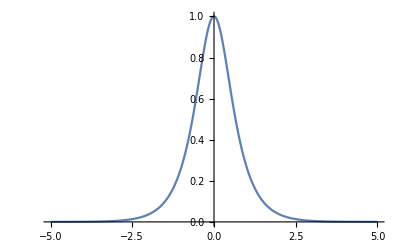

```mathematica
Plot[Sech[2 t],{t,-5,5}]
```

### derive STIRAP condition for 4 level system

Finding the dark eigenstate for 4-level STIRAP seems to be difficult in general.

```mathematica
Clear[Ωα,Ωβ,Ωγ,Δ1,Δ2]
H=({{0, Ωα/2, 0, 0}, {Ωα/2, Δ1, Ωβ/2, 0}, {0, Ωβ/2, Δ2, Ωγ/2}, {0, 0, Ωγ/2, 0}});
```

Diagonalizing H in general is super messy:

```mathematica
Assuming[{Ωα,Ωβ,Ωγ,Δ1,Δ2}∈Reals&&{Ωα,Ωβ,Ωγ,Δ1,Δ2}>0,Eigensystem[H]]//FullSimplify
```

{{1/2 Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,1],1/2 Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,2],1/2 Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,3],1/2 Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,4]},{{1/(Ωβ Ωγ)Ωα (-2 Δ2-Ωγ^2/Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,1]+Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,1]),1/(Ωβ Ωγ)(-Ωγ^2-2 Δ2 Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,1]+Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,1]^2),1/Ωγ Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,1],1},{1/(Ωβ Ωγ)Ωα (-2 Δ2-Ωγ^2/Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,2]+Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,2]),1/(Ωβ Ωγ)(-Ωγ^2-2 Δ2 Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,2]+Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,2]^2),1/Ωγ Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,2],1},{1/(Ωβ Ωγ)Ωα (-2 Δ2-Ωγ^2/Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,3]+Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,3]),1/(Ωβ Ωγ)(-Ωγ^2-2 Δ2 Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,3]+Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,3]^2),1/Ωγ Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,3],1},{1/(Ωβ Ωγ)Ωα (-2 Δ2-Ωγ^2/Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,4]+Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,4]),1/(Ωβ Ωγ)(-Ωγ^2-2 Δ2 Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,4]+Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,4]^2),1/Ωγ Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,4],1}}}

Try insisting the accumulated detunings 1 and 2 are the same. Nope, still messy and shows Root symbols.

```mathematica
{evals,evecs}=Assuming[{Ωα,Ωβ,Ωγ,Δ1}∈Reals&&{Ωα,Ωβ,Ωγ,Δ1}>0,Eigensystem[H/.Δ2->Δ1]]//FullSimplify
```

{{1/2 Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,1],1/2 Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,2],1/2 Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,3],1/2 Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,4]},{{1/(Ωβ Ωγ)Ωα (-2 Δ1-Ωγ^2/Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,1]+Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,1]),1/(Ωβ Ωγ)(-Ωγ^2-2 Δ1 Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,1]+Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,1]^2),Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,1]/Ωγ,1},{1/(Ωβ Ωγ)Ωα (-2 Δ1-Ωγ^2/Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,2]+Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,2]),1/(Ωβ Ωγ)(-Ωγ^2-2 Δ1 Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,2]+Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,2]^2),Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,2]/Ωγ,1},{1/(Ωβ Ωγ)Ωα (-2 Δ1-Ωγ^2/Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,3]+Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,3]),1/(Ωβ Ωγ)(-Ωγ^2-2 Δ1 Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,3]+Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,3]^2),Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,3]/Ωγ,1},{1/(Ωβ Ωγ)Ωα (-2 Δ1-Ωγ^2/Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,4]+Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,4]),1/(Ωβ Ωγ)(-Ωγ^2-2 Δ1 Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,4]+Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,4]^2),Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,4]/Ωγ,1}}}

Relax the real constraint. Nope.

```mathematica
Assuming[{Ωα,Ωβ,Ωγ,Δ1,Δ2},Eigensystem[H]]//FullSimplify
```

{{1/2 Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,1],1/2 Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,2],1/2 Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,3],1/2 Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,4]},{{1/(Ωβ Ωγ)Ωα (-2 Δ2-Ωγ^2/Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,1]+Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,1]),1/(Ωβ Ωγ)(-Ωγ^2-2 Δ2 Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,1]+Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,1]^2),Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,1]/Ωγ,1},{1/(Ωβ Ωγ)Ωα (-2 Δ2-Ωγ^2/Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,2]+Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,2]),1/(Ωβ Ωγ)(-Ωγ^2-2 Δ2 Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,2]+Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,2]^2),Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,2]/Ωγ,1},{1/(Ωβ Ωγ)Ωα (-2 Δ2-Ωγ^2/Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,3]+Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,3]),1/(Ωβ Ωγ)(-Ωγ^2-2 Δ2 Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,3]+Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,3]^2),Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,3]/Ωγ,1},{1/(Ωβ Ωγ)Ωα (-2 Δ2-Ωγ^2/Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,4]+Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,4]),1/(Ωβ Ωγ)(-Ωγ^2-2 Δ2 Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,4]+Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,4]^2),Root[Ωα^2 Ωγ^2+(2 Δ2 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1 Δ2-Ωα^2-Ωβ^2-Ωγ^2) #1^2+(-2 Δ1-2 Δ2) #1^3+#1^4&,4]/Ωγ,1}}}

Relax the real constraint and maintain the same detunings. Nope.

```mathematica
Assuming[{Ωα,Ωβ,Ωγ,Δ1,Δ2},Eigensystem[H/.Δ2->Δ1]]//FullSimplify
```

{{1/2 Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,1],1/2 Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,2],1/2 Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,3],1/2 Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,4]},{{1/(Ωβ Ωγ)Ωα (-2 Δ1-Ωγ^2/Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,1]+Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,1]),1/(Ωβ Ωγ)(-Ωγ^2-2 Δ1 Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,1]+Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,1]^2),Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,1]/Ωγ,1},{1/(Ωβ Ωγ)Ωα (-2 Δ1-Ωγ^2/Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,2]+Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,2]),1/(Ωβ Ωγ)(-Ωγ^2-2 Δ1 Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,2]+Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,2]^2),Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,2]/Ωγ,1},{1/(Ωβ Ωγ)Ωα (-2 Δ1-Ωγ^2/Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,3]+Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,3]),1/(Ωβ Ωγ)(-Ωγ^2-2 Δ1 Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,3]+Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,3]^2),Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,3]/Ωγ,1},{1/(Ωβ Ωγ)Ωα (-2 Δ1-Ωγ^2/Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,4]+Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,4]),1/(Ωβ Ωγ)(-Ωγ^2-2 Δ1 Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,4]+Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,4]^2),Root[Ωα^2 Ωγ^2+(2 Δ1 Ωα^2+2 Δ1 Ωγ^2) #1+(4 Δ1^2-Ωα^2-Ωβ^2-Ωγ^2) #1^2-4 Δ1 #1^3+#1^4&,4]/Ωγ,1}}}

Diagonalize only for early times when Ωγ hasn’t kicked in and the detunings are the same.

```mathematica
Assuming[{Ωα,Ωβ,Δ1,Δ2}>0,Eigensystem[H/.{Ωγ->0,Δ2->Δ1}]]//FullSimplify
```

{{0,1/2 Root[2 Δ1 Ωα^2+(4 Δ1^2-Ωα^2-Ωβ^2) #1-4 Δ1 #1^2+#1^3&,1],1/2 Root[2 Δ1 Ωα^2+(4 Δ1^2-Ωα^2-Ωβ^2) #1-4 Δ1 #1^2+#1^3&,2],1/2 Root[2 Δ1 Ωα^2+(4 Δ1^2-Ωα^2-Ωβ^2) #1-4 Δ1 #1^2+#1^3&,3]},{{0,0,0,1},{(Ωα (1-(2 Δ1)/Root[2 Δ1 Ωα^2+(4 Δ1^2-Ωα^2-Ωβ^2) #1-4 Δ1 #1^2+#1^3&,1]))/Ωβ,(-2 Δ1+Root[2 Δ1 Ωα^2+(4 Δ1^2-Ωα^2-Ωβ^2) #1-4 Δ1 #1^2+#1^3&,1])/Ωβ,1,0},{(Ωα (1-(2 Δ1)/Root[2 Δ1 Ωα^2+(4 Δ1^2-Ωα^2-Ωβ^2) #1-4 Δ1 #1^2+#1^3&,2]))/Ωβ,(-2 Δ1+Root[2 Δ1 Ωα^2+(4 Δ1^2-Ωα^2-Ωβ^2) #1-4 Δ1 #1^2+#1^3&,2])/Ωβ,1,0},{(Ωα (1-(2 Δ1)/Root[2 Δ1 Ωα^2+(4 Δ1^2-Ωα^2-Ωβ^2) #1-4 Δ1 #1^2+#1^3&,3]))/Ωβ,(-2 Δ1+Root[2 Δ1 Ωα^2+(4 Δ1^2-Ωα^2-Ωβ^2) #1-4 Δ1 #1^2+#1^3&,3])/Ωβ,1,0}}}

Diagonalize only for late times when Ωα has turned off and the detunings are the same.

```mathematica
Assuming[{Ωβ,Ωγ,Δ1,Δ2}>0,Eigensystem[H/.{Ωα->0,Δ2->0}]]//FullSimplify
```

{{0,1/2 Root[2 Δ1 Ωγ^2+(-Ωβ^2-Ωγ^2) #1-2 Δ1 #1^2+#1^3&,1],1/2 Root[2 Δ1 Ωγ^2+(-Ωβ^2-Ωγ^2) #1-2 Δ1 #1^2+#1^3&,2],1/2 Root[2 Δ1 Ωγ^2+(-Ωβ^2-Ωγ^2) #1-2 Δ1 #1^2+#1^3&,3]},{{1,0,0,0},{0,(-Ωγ^2+Root[2 Δ1 Ωγ^2+(-Ωβ^2-Ωγ^2) #1-2 Δ1 #1^2+#1^3&,1]^2)/(Ωβ Ωγ),Root[2 Δ1 Ωγ^2+(-Ωβ^2-Ωγ^2) #1-2 Δ1 #1^2+#1^3&,1]/Ωγ,1},{0,(-Ωγ^2+Root[2 Δ1 Ωγ^2+(-Ωβ^2-Ωγ^2) #1-2 Δ1 #1^2+#1^3&,2]^2)/(Ωβ Ωγ),Root[2 Δ1 Ωγ^2+(-Ωβ^2-Ωγ^2) #1-2 Δ1 #1^2+#1^3&,2]/Ωγ,1},{0,(-Ωγ^2+Root[2 Δ1 Ωγ^2+(-Ωβ^2-Ωγ^2) #1-2 Δ1 #1^2+#1^3&,3]^2)/(Ωβ Ωγ),Root[2 Δ1 Ωγ^2+(-Ωβ^2-Ωγ^2) #1-2 Δ1 #1^2+#1^3&,3]/Ωγ,1}}}

Try parametrizing the first and last fields.

```mathematica
Clear[Ω0];
H=({{0, Ω0 Sin[ϕ]/2, 0, 0}, {Ω0 Sin[ϕ]/2, Δ1, Ωβ/2, 0}, {0, Ωβ/2, Δ2, Ω0 Cos[ϕ]/2}, {0, 0, Ω0 Cos[ϕ]/2, 0}});
Assuming[{Ω0,Ωβ,Δ1,Δ2,ϕ}>0,Eigensystem[H/.{Δ2->Δ1,Ωβ->Ω0/2}]]//FullSimplify
```

{{1/4 Root[2 Ω0^4-2 Ω0^4 Cos[4 ϕ]+16 Δ1 Ω0^2 #1+(16 Δ1^2-5 Ω0^2) #1^2-8 Δ1 #1^3+#1^4&,1],1/4 Root[2 Ω0^4-2 Ω0^4 Cos[4 ϕ]+16 Δ1 Ω0^2 #1+(16 Δ1^2-5 Ω0^2) #1^2-8 Δ1 #1^3+#1^4&,2],1/4 Root[2 Ω0^4-2 Ω0^4 Cos[4 ϕ]+16 Δ1 Ω0^2 #1+(16 Δ1^2-5 Ω0^2) #1^2-8 Δ1 #1^3+#1^4&,3],1/4 Root[2 Ω0^4-2 Ω0^4 Cos[4 ϕ]+16 Δ1 Ω0^2 #1+(16 Δ1^2-5 Ω0^2) #1^2-8 Δ1 #1^3+#1^4&,4]},{{-(4 Ω0 Cos[ϕ] Sin[ϕ])/Root[2 Ω0^4-2 Ω0^4 Cos[4 ϕ]+16 Δ1 Ω0^2 #1+(16 Δ1^2-5 Ω0^2) #1^2-8 Δ1 #1^3+#1^4&,1]+((-4 Δ1+Root[2 Ω0^4-2 Ω0^4 Cos[4 ϕ]+16 Δ1 Ω0^2 #1+(16 Δ1^2-5 Ω0^2) #1^2-8 Δ1 #1^3+#1^4&,1]) Tan[ϕ])/Ω0,-2 Cos[ϕ]+1/(2 Ω0^2)Root[2 Ω0^4-2 Ω0^4 Cos[4 ϕ]+16 Δ1 Ω0^2 #1+(16 Δ1^2-5 Ω0^2) #1^2-8 Δ1 #1^3+#1^4&,1] (-4 Δ1+Root[2 Ω0^4-2 Ω0^4 Cos[4 ϕ]+16 Δ1 Ω0^2 #1+(16 Δ1^2-5 Ω0^2) #1^2-8 Δ1 #1^3+#1^4&,1]) Sec[ϕ],(Root[2 Ω0^4-2 Ω0^4 Cos[4 ϕ]+16 Δ1 Ω0^2 #1+(16 Δ1^2-5 Ω0^2) #1^2-8 Δ1 #1^3+#1^4&,1] Sec[ϕ])/(2 Ω0),1},{-(4 Ω0 Cos[ϕ] Sin[ϕ])/Root[2 Ω0^4-2 Ω0^4 Cos[4 ϕ]+16 Δ1 Ω0^2 #1+(16 Δ1^2-5 Ω0^2) #1^2-8 Δ1 #1^3+#1^4&,2]+((-4 Δ1+Root[2 Ω0^4-2 Ω0^4 Cos[4 ϕ]+16 Δ1 Ω0^2 #1+(16 Δ1^2-5 Ω0^2) #1^2-8 Δ1 #1^3+#1^4&,2]) Tan[ϕ])/Ω0,-2 Cos[ϕ]+1/(2 Ω0^2)Root[2 Ω0^4-2 Ω0^4 Cos[4 ϕ]+16 Δ1 Ω0^2 #1+(16 Δ1^2-5 Ω0^2) #1^2-8 Δ1 #1^3+#1^4&,2] (-4 Δ1+Root[2 Ω0^4-2 Ω0^4 Cos[4 ϕ]+16 Δ1 Ω0^2 #1+(16 Δ1^2-5 Ω0^2) #1^2-8 Δ1 #1^3+#1^4&,2]) Sec[ϕ],(Root[2 Ω0^4-2 Ω0^4 Cos[4 ϕ]+16 Δ1 Ω0^2 #1+(16 Δ1^2-5 Ω0^2) #1^2-8 Δ1 #1^3+#1^4&,2] Sec[ϕ])/(2 Ω0),1},{-(4 Ω0 Cos[ϕ] Sin[ϕ])/Root[2 Ω0^4-2 Ω0^4 Cos[4 ϕ]+16 Δ1 Ω0^2 #1+(16 Δ1^2-5 Ω0^2) #1^2-8 Δ1 #1^3+#1^4&,3]+((-4 Δ1+Root[2 Ω0^4-2 Ω0^4 Cos[4 ϕ]+16 Δ1 Ω0^2 #1+(16 Δ1^2-5 Ω0^2) #1^2-8 Δ1 #1^3+#1^4&,3]) Tan[ϕ])/Ω0,-2 Cos[ϕ]+1/(2 Ω0^2)Root[2 Ω0^4-2 Ω0^4 Cos[4 ϕ]+16 Δ1 Ω0^2 #1+(16 Δ1^2-5 Ω0^2) #1^2-8 Δ1 #1^3+#1^4&,3] (-4 Δ1+Root[2 Ω0^4-2 Ω0^4 Cos[4 ϕ]+16 Δ1 Ω0^2 #1+(16 Δ1^2-5 Ω0^2) #1^2-8 Δ1 #1^3+#1^4&,3]) Sec[ϕ],(Root[2 Ω0^4-2 Ω0^4 Cos[4 ϕ]+16 Δ1 Ω0^2 #1+(16 Δ1^2-5 Ω0^2) #1^2-8 Δ1 #1^3+#1^4&,3] Sec[ϕ])/(2 Ω0),1},{-(4 Ω0 Cos[ϕ] Sin[ϕ])/Root[2 Ω0^4-2 Ω0^4 Cos[4 ϕ]+16 Δ1 Ω0^2 #1+(16 Δ1^2-5 Ω0^2) #1^2-8 Δ1 #1^3+#1^4&,4]+((-4 Δ1+Root[2 Ω0^4-2 Ω0^4 Cos[4 ϕ]+16 Δ1 Ω0^2 #1+(16 Δ1^2-5 Ω0^2) #1^2-8 Δ1 #1^3+#1^4&,4]) Tan[ϕ])/Ω0,-2 Cos[ϕ]+1/(2 Ω0^2)Root[2 Ω0^4-2 Ω0^4 Cos[4 ϕ]+16 Δ1 Ω0^2 #1+(16 Δ1^2-5 Ω0^2) #1^2-8 Δ1 #1^3+#1^4&,4] (-4 Δ1+Root[2 Ω0^4-2 Ω0^4 Cos[4 ϕ]+16 Δ1 Ω0^2 #1+(16 Δ1^2-5 Ω0^2) #1^2-8 Δ1 #1^3+#1^4&,4]) Sec[ϕ],(Root[2 Ω0^4-2 Ω0^4 Cos[4 ϕ]+16 Δ1 Ω0^2 #1+(16 Δ1^2-5 Ω0^2) #1^2-8 Δ1 #1^3+#1^4&,4] Sec[ϕ])/(2 Ω0),1}}}

### misc

Pulse area. just √(Ω_1^2+Ω_2^2), integrated over +- infinity?

```mathematica
Integrate[Exp[(-(t-μ/2)^2)/(2 w^2)]Exp[(-(t+μ/2)^2)/(2 w^2)]
```

```mathematica
Exp[(-(t-μ/2)^2)/(2 w^2)]Exp[(-(t+μ/2)^2)/(2 w^2)]//Simplify
```

ⅇ^(-(4 t^2+μ^2)/(4 w^2))

```mathematica
ⅇ^(-μ^2/(4 w^2))ⅇ^(-t^2/w^2)
```

Calculate the derivative of R in the torque picture

```mathematica
Clear[ϕ,θ,R,Γ,Ω1,Ω2,Δ1,Δ2]
R={c1,c2,c3};
Γ={Ω2,0,-Ω1};
Cross[Γ,R]
```

{c2 Ω1,-c1 Ω1-c3 Ω2,c2 Ω2}

```mathematica
H=({{0, Ω1/2, 0}, {Ω1/2, Δ1, Ω2/2}, {0, Ω2/2, Δ1+Δ2}})
```

{{0,Ω1/2,0},{Ω1/2,Δ1,Ω2/2},{0,Ω2/2,Δ1+Δ2}}

```mathematica
Assuming[Ω1∈Reals&&Ω2∈Reals&&Δ1∈Reals&&Δ2∈Reals,Eigensystem[H]]//FullSimplify
```

{{1/2 Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,1],1/2 Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,2],1/2 Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,3]},{{(Ω1 (1-(2 (Δ1+Δ2))/Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,1]))/Ω2,1/Ω2(-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,1]),1},{(Ω1 (1-(2 (Δ1+Δ2))/Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,2]))/Ω2,1/Ω2(-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,2]),1},{(Ω1 (1-(2 (Δ1+Δ2))/Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,3]))/Ω2,1/Ω2(-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,3]),1}}}

```mathematica
FullSimplify[#/√(#.#),Assumptions->{Ω1∈Reals,Ω2∈Reals}]&/@Eigensystem[H][[2]]
```

{{(Ω1 (-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,1]))/(Ω2 Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,1] √(1+1/Ω2^2(-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,1])^2+(Ω1^2 (-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,1])^2)/(Ω2^2 Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,1]^2))),(-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,1])/(Ω2 √(1+1/Ω2^2(-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,1])^2+(Ω1^2 (-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,1])^2)/(Ω2^2 Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,1]^2))),1/(√(1+1/Ω2^2(-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,1])^2+(Ω1^2 (-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,1])^2)/(Ω2^2 Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,1]^2)))},{(Ω1 (-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,2]))/(Ω2 Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,2] √(1+1/Ω2^2(-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,2])^2+(Ω1^2 (-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,2])^2)/(Ω2^2 Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,2]^2))),(-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,2])/(Ω2 √(1+1/Ω2^2(-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,2])^2+(Ω1^2 (-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,2])^2)/(Ω2^2 Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,2]^2))),1/(√(1+1/Ω2^2(-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,2])^2+(Ω1^2 (-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,2])^2)/(Ω2^2 Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,2]^2)))},{(Ω1 (-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,3]))/(Ω2 Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,3] √(1+1/Ω2^2(-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,3])^2+(Ω1^2 (-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,3])^2)/(Ω2^2 Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,3]^2))),(-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,3])/(Ω2 √(1+1/Ω2^2(-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,3])^2+(Ω1^2 (-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,3])^2)/(Ω2^2 Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,3]^2))),1/(√(1+1/Ω2^2(-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,3])^2+(Ω1^2 (-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,3])^2)/(Ω2^2 Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,3]^2)))}}

```mathematica
ReplaceAll[{-Ω2/(Ω1 √(2+(2 Ω1^2)/Ω2^2)),0,1/(√(2+(2 Ω1^2)/Ω2^2))},Ω1/Ω2-> ArcTan[Θ]]
```

{-Ω2/(Ω1 √(2+(2 Ω1^2)/Ω2^2)),0,1/(√(2+(2 Ω1^2)/Ω2^2))}

```mathematica
{(-Cos[x]^2)/(√2 Sin[x]),0,Cos[x]/(√2)}.{(-Cos[x]^2)/(√2 Sin[x]),0,Cos[x]/(√2)}//FullSimplify
```

Cot[x]^2/2